# Neutral atoms/Rydberg qubits

## Consultants : Natalie Pearson, Tomas Kozlej, Gerard Pelergi, Jonathan Pritchard, Andrew Daley

Set environment, such as threads, gpu, etc.

```mathematica
SetEnvironment["OMP_NUM_THREADS"->"8"]
SetDirectory[NotebookDirectory[]];
```

Load the QuESTLink. Now it works as well directly using the default pre-compiled binary. But it usea only single core.

```mathematica
Import["~/programs/QuESTlink/Link/QuESTlink.m"];
CreateLocalQuESTEnv["quest_link_cpu"];
```

Virtual quantum devices, loaded after questlink

```mathematica
Get["../vqd.wl"]
```

Time unit : μs
Frequency unit: MHz
Length unit: μm

Accepts 2 or 3 dimensional coordinate format

```mathematica
(* 2d-array of 9 atoms*)
locs2=Association@MapThread[#->#2&,{Range[0,8],Flatten[Table[{i,j},{i,0,2},{j,0,2}],1]}];
(* 3d-array of 27 atoms *)
locs3=Association@MapThread[#->#2&,{Range[0,26],Flatten[Table[{i,j,k},{i,0,2},{j,0,2},{k,0,2}],2]}];
```

Specification of the device by default. These can be changed on the fly by command RydbergHub[option → value]

## Default setting

```mathematica
Options[RydbergHub]={
(* The total number of atoms/qubit*)
QubitNum ->  9
,
(*Physical location on each qubit described with a 2D- or 3D-vector*)
AtomLocations -> locs2
,
(* It's presumed that Subscript[T, 2]^* has been echoed out to Subscript[T, 2] *)
T2 -> 100*10^6
,
(* The life time of vacuum chamber, where it affects the coherence time: T1=τvac/N -- in μs *)
VacLifeTime -> 100*10^6
,
(* Rabi frequency of the atoms in MHz. We assume the duration of multi-qubit gates is as long as 4π pulse of single-qubit gates *)
RabiFreq -> 0.1
,
(* Asymmetric bit-flip error probability; the error is acquired during single qubit operation *)
ProbBFRot -> <|10->0.015, 01->0.025|>
,
(* Unit lattice in μm. This will be the unit of the lattice/locations given in qubitLocations *)
UnitLattice -> Sqrt@2
,
(* blockade radius in μm *)
BlockadeRadius -> Sqrt@2
,
(* The factor that estimates accelerated dephasing due to moving the atoms. Ideally, it is calculated from the distance and speed. *)
HeatFactor -> 10
,
(* Leakage probability during initalisation process *)
ProbLeakInit -> 0.01
,
(* duration of moving atoms; we assume SWAPLoc and ShiftLoc take this amount of time: 100 μs *)
DurMove -> 100
,
(* duration of lattice initialization which involves the atom loading (~50%) and rearranging the optical tweezer *)
DurInit -> 5*10^5
,
(* measurement fidelity and duration, were it induces atom loss afterward *)
FidMeas -> 0.987
,
DurMeas -> 10
,
(* The increasing probability of atom loss on each measurement. The value keeps increasing until being initialised *)
ProbLossMeas -> 0.05
,
(* leak probability of implementing multi-qubit gates *)
ProbLeakCZ -> <|01-> 0.001,11->0.001 |>
};
```

## Elementary guide

### Native gates

(* initialisation and readout *)
Init_q, M_q
(* single-qubit gates *)
Rx_q[θ], Ry_q[θ], Rz_q[θ], H_q, SRot_q[ϕ, Δ, Δt] 
(* two-qubit gate *)
CZ_(q1,q2)[ϕ] 
(* multi-qubit gates *)
C_(q1,q2,q3,...)[Z_qt], C_c[Z_(q1,q2,q3,...)]
(* reconfiguring atom locations *)
SWAPLoc_(q1,q2), ShiftLoc_(q1,q2,...)[v]
(* others: wait or doing nothing *)
Wait_q[Δt]

## Elementary guide

### The 2D- and 3D- dimensional arrays

```mathematica
device1=RydbergHub[];
```

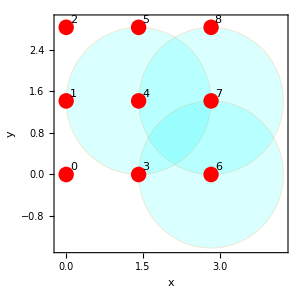

```mathematica
PlotAtoms[device1,ImageSize->300,BaseStyle->Directive[18,FontFamily->"Times"],ShowBlockade->{4,7,6}]
```

```mathematica
device2=RydbergHub[T2->10^5,QubitNum->27,AtomLocations->locs3];
```

```mathematica
PlotAtoms[device2,ImageSize->Large,BaseStyle->Directive[18,FontFamily->"Times"],ShowBlockade->{0,9}]
```

-Graphics3D-

## The essential functionalities on the virtual device

RydbergHub[] creates an instance of the virtual device with the default parameters given above.
Use OptionValue[RydbergHub, option] to check the default value of option of the RydbergHub finction.

One can also check on the used options device[UsedOptions] when generating the device

```mathematica
dev=RydbergHub[];
```

```mathematica
OptionValue[RydbergHub,ProbLeakInit]
```

0.01

```mathematica
dev[OptionsUsed]
```

{QubitNum→9,AtomLocations→<|0→{0,0},1→{0,1},2→{0,2},3→{1,0},4→{1,1},5→{1,2},6→{2,0},7→{2,1},8→{2,2}|>,T2→100000000,VacLifeTime→100000000,RabiFreq→0.1,ProbBFRot→<|10→0.015,1→0.025|>,UnitLattice→√2,BlockadeRadius→√2,ProbLeakInit→0.01,DurInit→500000,FidMeas→0.987,DurMeas→10,DurMove→100,ProbLossMeas→0.05,ProbLeakCZ→<|1→0.001,11→0.001|>}

### Show the atoms and reconfiguring the register: PlotAtoms[]

Spatial locations accept 2D and 3D arrangements. Set  ShowBlockade → {qubits} to show the blockade radius.
Use command Options[function], to see what options that are available to a function. 
Also type ?function to see a short help about the function.

```mathematica
Options@PlotAtoms
```

{ShowBlockade→{},ShowLossAtoms→False}

Here we change the number of qubits, location, and the unit of lattice on the fly

```mathematica
locs=Association@MapThread[#->#2&,{Range[0,7],Flatten[Table[{i,j,k},{i,0,1},{j,0,1},{k,0,1}],2]}]
```

<|0→{0,0,0},1→{0,0,1},2→{0,1,0},3→{0,1,1},4→{1,0,0},5→{1,0,1},6→{1,1,0},7→{1,1,1}|>

Atoms cannot be moved if place is occupied alread. Notice that the atoms moved experience enhance dephasing

```mathematica
dev3=RydbergHub[QubitNum->8,AtomLocations->locs,ProbLossMeas->1, UnitLattice->2.1];
InsertCircuitNoise[{Subscript[ShiftLoc, 1,7][{1,0,0}]},dev3]
```

InsertCircuitNoise::error: Encountered gate ShiftLoc_(1,7)[{1,0,0}] which is not supported by the given device specification. Note this may be due to preceding gates, if the spec contains constraints which depend on dynamic variables. See ?GetUnsupportedGates.

$Failed

```mathematica
dev3=RydbergHub[QubitNum->8,AtomLocations->locs,ProbLossMeas->1, UnitLattice->2.1];
InsertCircuitNoise[{Subscript[ShiftLoc, 1,7][{-.5,.5,0}]},dev3]
```

{{0,{Depol_1[5.99998×10^-6],Deph_1[4.99998×10^-6],Depol_7[5.99998×10^-6],Deph_7[4.99998×10^-6]},{Depol_0[5.99998×10^-6],Deph_0[5.×10^-7],Depol_1[0.],Deph_1[0.],Depol_2[5.99998×10^-6],Deph_2[5.×10^-7],Depol_3[5.99998×10^-6],Deph_3[5.×10^-7],Depol_4[5.99998×10^-6],Deph_4[5.×10^-7],Depol_5[5.99998×10^-6],Deph_5[5.×10^-7],Depol_6[5.99998×10^-6],Deph_6[5.×10^-7],Depol_7[0.],Deph_7[0.]}}}

```mathematica
PlotAtoms[dev3]
```

-Graphics3D-

One can modify the plots using Graphics options

```mathematica
Options@PlotAtoms
```

{ShowBlockade→{},ShowLossAtoms→False}

```mathematica
Options@Graphics
```

{AlignmentPoint→Center,AspectRatio→Automatic,Axes→False,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},FormatType:>TraditionalForm,Frame→False,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,LabelStyle→{},Method→Automatic,PlotLabel→None,PlotRange→All,PlotRangeClipping→False,PlotRangePadding→Automatic,PlotRegion→Automatic,PreserveImageOptions→Automatic,Prolog→{},RotateLabel→True,Ticks→Automatic,TicksStyle→{}}

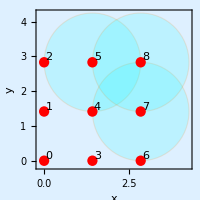

```mathematica
PlotAtoms[RydbergHub[UnitLattice->Sqrt[2]],ShowBlockade->{5,7,8},ImageSize->200,Background->LightBlue]
```

## Native gates of the device

[Native gates]

 Init, Wait_q__, Read, M, SRot, H, Rx[θ], Ry[θ], Rz[θ], SWAPLoc, ShiftLoc, CZ_(q1,q2,...),C[Z[θ]], C[Z]

## Arbitrary single rotation

Hadamard: ϕ→0,Δ→Ω,t→π/Ω̃

Here, I assign Ω with the default value of RabiFreq for practicality. Then I check what matrix produced with SRot[] gate given value.
I access Aliases definition to replace SRot[] definition since it is not a native QuESTLink gate by replace command /.

```mathematica
Ω=OptionValue[RydbergHub,RabiFreq]
```

0.1

```mathematica
CalcCircuitMatrix[Subscript[SRot, 0][0,Ω,π/Sqrt[2 Ω^2]]/.RydbergHub[][Aliases]]//Chop//MatrixForm
```

(0.-0.707107 ⅈ | 0.-0.707107 ⅈ
0.-0.707107 ⅈ | 0.+0.707107 ⅈ)

Rotation around x-axis  via  SRot[ϕ→0,Δ→0,t→θ/Ω ] or directly using Rx[θ].

Chop[] is called to remove the thrilling zeros

```mathematica
CalcCircuitMatrix[Subscript[Rx, 0][π/Ω]]//MatrixForm
```

(-1.+0. ⅈ | 0.-6.12323×10^-16 ⅈ
0.-6.12323×10^-16 ⅈ | -1.+0. ⅈ)

```mathematica
CalcCircuitMatrix[Subscript[Rx, 0][π]]//Chop//MatrixForm
```

(0 | -ⅈ
-ⅈ | 0)

```mathematica
CalcCircuitMatrix[Subscript[SRot, 0][0,0,π/Ω]/.RydbergHub[][Aliases]]//Chop//MatrixForm
```

(0 | 0.-1. ⅈ
0.-1. ⅈ | 0)

## Multi-qubit gates must fulfill blockade requirement

The operation controlled-Z up to a single qubit phase ϕ : inside blockade vs outside blockade

```mathematica
CalcCircuitMatrix[Subscript[CZ, 0,1][ϕ]/.RydbergHub[][Aliases]]//MatrixForm
```

(1 | 0 | 0 | 0
0 | ⅇ^(ⅈ ϕ) | 0 | 0
0 | 0 | ⅇ^(ⅈ ϕ) | 0
0 | 0 | 0 | ⅇ^(ⅈ (-π+2 ϕ)))

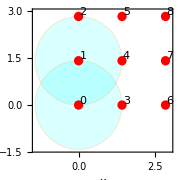

```mathematica
PlotAtoms[RydbergHub[],ShowBlockade->{0,1},ImageSize->Small]
```

```mathematica
InsertCircuitNoise[{Subscript[CZ, 0,1][ϕ]},device1]
```

{{0,{CZ_(0,1)[ϕ],KrausNonTP_(0,1)[{{{1,0,0,0},{0,0.9995,0,0},{0,0,0.9995,0},{0,0,0,0.9995}}}]},{Depol_0[0.],Deph_0[0.],Depol_1[0.],Deph_1[0.],Depol_2[8.48225×10^-6],Deph_2[6.28318×10^-7],Depol_3[8.48225×10^-6],Deph_3[6.28318×10^-7],Depol_4[8.48225×10^-6],Deph_4[6.28318×10^-7],Depol_5[8.48225×10^-6],Deph_5[6.28318×10^-7],Depol_6[8.48225×10^-6],Deph_6[6.28318×10^-7],Depol_7[8.48225×10^-6],Deph_7[6.28318×10^-7],Depol_8[8.48225×10^-6],Deph_8[6.28318×10^-7]}}}

The device dev below has a more separated lattice. The blockade radius do not overlap, thus CZ_(0,1)[ϕ] gate application becomes illegal and returns error.

```mathematica
dev=RydbergHub[UnitLattice->0.00001+2√2];
```

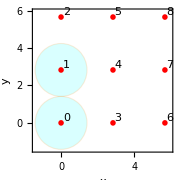

```mathematica
PlotAtoms[dev,ShowBlockade->{0,1},ImageSize->Small]
```

```mathematica
InsertCircuitNoise[{Subscript[CZ, 0,1][ϕ]},dev]
```

InsertCircuitNoise::error: Encountered gate CZ_(0,1)[ϕ] which is not supported by the given device specification. Note this may be due to preceding gates, if the spec contains constraints which depend on dynamic variables. See ?GetUnsupportedGates.

$Failed

Multiqubit gates C_c__[Z_t__] or C_c__[Z_t__] , every qubit in cq and tq must be overlapping each other in the blockade radius.
In the following example, qubits{ 0,1,3,4} , { 3,4,6,7}, {5,4,7,8 }have overlapping blockade radius; they must produce legit multi-qubit gates.
side note: Variable j_ accepts input with 1 entry. j__ accepts input with at least one entry

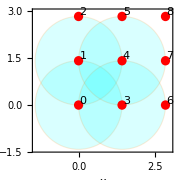

```mathematica
PlotAtoms[RydbergHub[],ShowBlockade->{0,1,3,4},ImageSize->Small]
```

```mathematica
PlotAtoms[RydbergHub[],ShowBlockade->{0,1,3,4},ImageSize->Small]
```

-Graphics-

```mathematica
InsertCircuitNoise[{Subscript[C, 0][Subscript[Z, 1,3,4]],Subscript[C, 4][Subscript[Z, 3,6,7]],Subscript[C, 4,5,7][Subscript[Z, 8]],Subscript[C, 2,5][Subscript[Z, 4]]},RydbergHub[]];
```

variable % is useful to pass the outcome of previous executed command

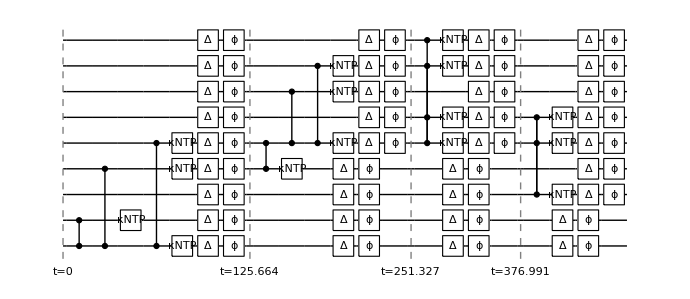

```mathematica
DrawCircuit@%
```

## Operations outside native gates and how to verify

We can define an arbitrary gates above this layer straightforwardly using ReplaceAll[]. For example, I will replace simple Toffoli (where the last qubit becomes the target) with Rydberg native multi-z gate and hadamard.

```mathematica
gateRule={Subscript[Toff, q__]:>With[{c=Sequence@@({q}[[;;-2]]),t=Last@{q}},{Subscript[H, t],Subscript[C, c][Subscript[Z, t]],Subscript[H, t]}]};
```

```mathematica
circ={Subscript[Toff, 0,1,2],Subscript[Toff, 2,3,4,5],Subscript[Toff, 0,1,2,3,4,5]};
DrawCircuit[%]
```

-Graphics-

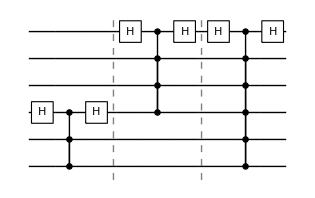

```mathematica
DrawCircuit[circ/.gateRule]
```

Note that, quest is using Least significant bit! so be careful with the indices!

For example, in the case of CNOT gate one commonly sees:
(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0)
that is because the indices  arranged from behind: {q0q1...qn}, e.g matrix above has basis  {00,01,10,11}. QuEST arrangement is {qn...q1q0}! Thus, instead, you will see

```mathematica
cnot=CalcCircuitMatrix[Subscript[C, 0][Subscript[X, 1]]];
```

```mathematica
cnot//MatrixForm
```

(1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0)

For instance, here is my function to rearrange the matrix to looks like the commonly defined order

```mathematica
rearrange[mat_]:=With[{d=Length@mat,nq=Log2[Length@mat]},
Table[mat[[Sequence@@(1+{FromDigits[Reverse@IntegerDigits[r,2,nq],2],FromDigits[Reverse@IntegerDigits[c,2,nq],2]})]],{r,0,d-1},{c,0,d-1}]
]
```

```mathematica
rearrange[cnot]//MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0)

Before rearrange

```mathematica
CalcCircuitMatrix[Subscript[Toff, 0,1,2,3]/.gateRule]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

After rearrange

```mathematica
CalcCircuitMatrix[Subscript[Toff, 0,1,2,3]/.gateRule]//rearrange//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0)

## Spatial operations

We can do consecutive commands. The instance dev will store previous state from the lass InsertCircuitNoise[] call.

```mathematica
dev=RydbergHub[];
```

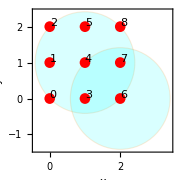

```mathematica
PlotAtoms[dev, ImageSize->Small,ShowBlockade->{4,6}]
```

```mathematica
InsertCircuitNoise[{Subscript[ShiftLoc, 0,1,2][{0,0.5}],Subscript[SWAPLoc, 8,7],Subscript[Wait, 0][.1],Subscript[ShiftLoc, 7,8,6][{0,-0.5}],Subscript[SWAPLoc, 4,6]},dev];
```

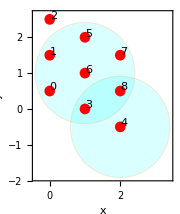

```mathematica
PlotAtoms[dev, ImageSize->Small,ShowBlockade->{4,6}]
```

```mathematica
InsertCircuitNoise[{Subscript[ShiftLoc, 7,8,4][{0.5,0}]},dev];
```

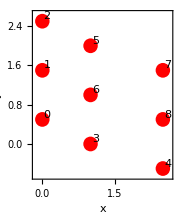

```mathematica
PlotAtoms[dev,ImageSize->Small]
```

## Scheduling : Rearrange circuit by parallel and serial

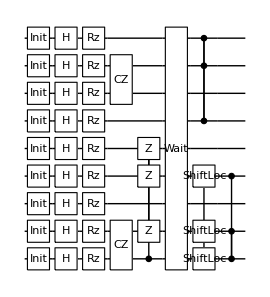

```mathematica
circ=Flatten@{{Subscript[Init, #],Subscript[H, #],Subscript[Rz, #][π/(#+1)]}&/@Range[0,8],Subscript[CZ, 6,7][π],Subscript[CZ, 0,1][π],Subscript[C, 0][Subscript[Z, 1,3,4]],Subscript[Wait, Range[0,8]][ϕ],Subscript[ShiftLoc, 0,1,3][{-1,0}],Subscript[C, 0,1][Subscript[Z, 3]],Subscript[C, 5,8][Subscript[Z, 7]]};
DrawCircuit@%
```

Parallel excution, where paralellism applies when the operations are done without non-overlaping blockade radius (future)
At the moment, it applies when it is not a multi-qubit gate. But initialisation is in parallel in nature.

```mathematica
Options@CircRydbergHub
```

{Parallel→False}

```mathematica
serialcirc=CircRydbergHub[circ,RydbergHub[]];
```

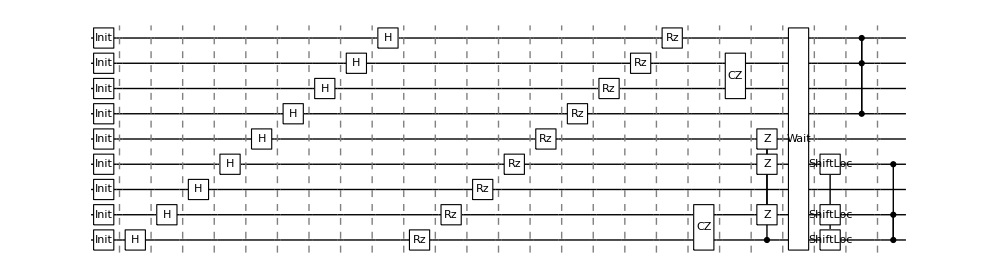

```mathematica
DrawCircuit@serialcirc
```

Serial excution. We rearrange a list of gates into a list of list {{... }, {...}, ... }.
The gates within the same inner list { ... } are executed in parallel. The schedule time is taken based on the maximal duration of the gates among the inner list.
One may edit this manually.

```mathematica
dev=RydbergHub[];
```

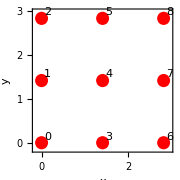

```mathematica
PlotAtoms[dev,ImageSize->Small]
```

```mathematica
parallelcirc=CircRydbergHub[circ,dev,Parallel->True]
```

{{Init_0,Init_1,Init_2,Init_3,Init_4,Init_5,Init_6,Init_7,Init_8},{H_0,H_1,H_2,H_3,H_4,H_5,H_6,H_7,H_8},{Rz_0[π],Rz_1[π/2],Rz_2[π/3],Rz_3[π/4],Rz_4[π/5],Rz_5[π/6],Rz_6[π/7],Rz_7[π/8],Rz_8[π/9]},{CZ_(6,7)[π]},{CZ_(0,1)[π]},{C_0[Z_(1,3,4)]},{Wait_{0,1,2,3,4,5,6,7,8}[ϕ]},{ShiftLoc_(0,1,3)[{-1,0}]},{C_(5,8)[Z_7]},{C_(0,1)[Z_3]}}

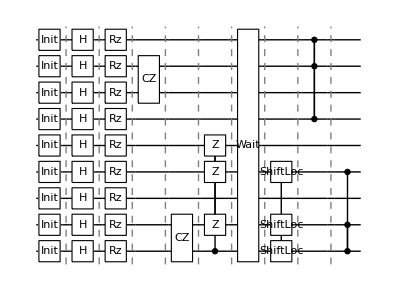

```mathematica
DrawCircuit@%
```

For example, I execute the hadamards in pair for some reason.

```mathematica
serialcirc2={{Subscript[Init, 0],Subscript[Init, 1],Subscript[Init, 2],Subscript[Init, 3],Subscript[Init, 4],Subscript[Init, 5],Subscript[Init, 6],Subscript[Init, 7],Subscript[Init, 8]},{Subscript[H, 0],Subscript[H, 1]},{Subscript[H, 2],Subscript[H, 3]},{Subscript[H, 4],Subscript[H, 5]},{Subscript[H, 6],Subscript[H, 7]},{Subscript[H, 8]},{Subscript[Rz, 0][π]},{Subscript[Rz, 1][π/2]},{Subscript[Rz, 2][π/3]},{Subscript[Rz, 3][π/4]},{Subscript[Rz, 4][π/5]},{Subscript[Rz, 5][π/6]},{Subscript[Rz, 6][π/7]},{Subscript[Rz, 7][π/8]},{Subscript[Rz, 8][π/9]},{Subscript[CZ, 0,1][π]},{Subscript[CZ, 6,7][π]},{Subscript[C, 0][Subscript[Z, 1,3,4]]},{Subscript[Wait, {0,1,2,3,4,5,6,7,8}][ϕ]},{Subscript[ShiftLoc, 0,1,3][{-1,0}]},{Subscript[C, 5,8][Subscript[Z, 7]]},{Subscript[C, 0,1][Subscript[Z, 3]]}};
```

Get noise-decorated circuit from rearranged circuit, where hadamard are run in pairs, in parallel

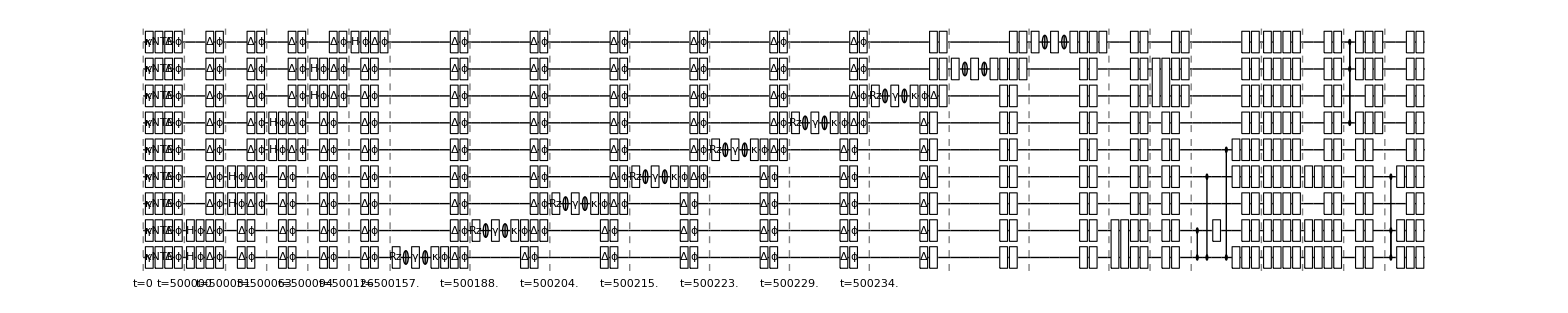

```mathematica
DrawCircuit@InsertCircuitNoise[serialcirc2,RydbergHub[]]
```

## Quantum simulation: 9-GHZ

```mathematica
ghz={
Subscript[Init, 0],Subscript[Init, 1],Subscript[Init, 2],Subscript[Init, 3],Subscript[Init, 4],Subscript[Init, 5],Subscript[Init, 6],Subscript[Init, 7],Subscript[Init, 8],
Subscript[H, 0],
Subscript[H, 1],Subscript[H, 3],Subscript[H, 4], Subscript[C, 0][Subscript[Z, 1,3,4]],Subscript[H, 1],Subscript[H, 3],Subscript[H, 4],
Subscript[H, 6],Subscript[H, 7],Subscript[C, 3][Subscript[Z, 6,7]],Subscript[H, 6],Subscript[H, 7],
Subscript[H, 5],Subscript[H, 8],Subscript[C, 7][Subscript[Z, 5,8]],Subscript[H, 5],Subscript[H, 8],
Subscript[H, 2],Subscript[C, 1][Subscript[Z, 2]],Subscript[H, 2]
};
```

```mathematica
(* allocate memory *)
ψ=CreateQureg[9];
ρ=CreateDensityQureg[9];
```

The non-native questlink gates are defined in the Aliases, so we need to replace those aliases into the native questlink gates. Apply the circuit in the state vector, noiseless case

```mathematica
ApplyCircuit[InitZeroState@ψ,Flatten[ghz/.dev[Aliases]]];
```

Initialise the qubits in a  random mixed state: extremely low fidelity. Note that CalcFidelity accepts density matrix and state vector. It cannot compare two density matrices.

```mathematica
SetQuregMatrix[ρ,RandomMixState[9]];
CalcFidelity[ρ,ψ]
```

0.0020333

Then apply the circuit in serial manner

```mathematica
ApplyCircuit[ρ,ExtractCircuit@InsertCircuitNoise[CircRydbergHub[ghz,RydbergHub[],Parallel->False],RydbergHub[]]];
```

```mathematica
CalcFidelity[ρ,ψ]
```

0.907664

Some trick on  approximating symmetric bit-flip error, implemeted in single qubit gate error

```mathematica
bf10=0.015;
bf01=0.025;
(* Since the outputs are favored to state 1, the remaining error is damping to state 1 
Here, we assume damping and bitflip are independent events. 
P(damp or bf)=P(damp)+P(bf)-P(damp)P(bf)
*)
damp1=First[p/.Solve[p+bf10-bf10 p==bf01,{p}]]
```

0.0101523

```mathematica
VQD`Private`bitFlip1[bf10]
```

{{{0.122474,0.},{0.,0.122474}},{{0.,0.992472},{0.992472,0.}}}

```mathematica
ρ1=CreateDensityQureg[1];
```

```mathematica
ApplyCircuit[InitZeroState@ρ1,{Subscript[X, 0],Subscript[Damp, 0][damp1],Subscript[X, 0],Subscript[Kraus, 0][VQD`Private`bitFlip1[1-bf10]]}];
Print["p(0->1)=",Re@GetQuregMatrix[ρ1][[2,2]]]
ApplyCircuit[InitZeroState@ρ1,{Subscript[Damp, 0][damp1],Subscript[X, 0],Subscript[Kraus, 0][VQD`Private`bitFlip1[1-bf10]]}];
Print["p(1->0)=",Re@GetQuregMatrix[ρ1][[1,1]]]
```

p(0->1)=0.0248477

p(1->0)=0.015

## Graph state generation

Source : www.nature.com/articles/s41586-022-04592-6

```mathematica
DestroyAllQuregs[];
ρ=CreateDensityQureg[12];
ρinit=CreateDensityQureg[12];
ρwork=CreateDensityQureg[12];
```

```mathematica
(*returns graph state stabilizer of a node*)
stabgs[graph_,node_]:=With[{neig=Complement[VertexList@NeighborhoodGraph[graph,node],{node}]},
ToExpression[StringRiffle[Join[{Subscript[X, node]},Subscript[Z, #]&/@neig]]]]
```

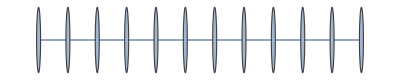

```mathematica
g=Graph[#<->#+1&/@Range[0,10]]
```

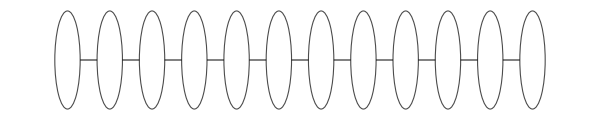

~/vqd/img/graph1d.pdf

```mathematica
Graph[g,VertexSize->0.6,VertexStyle->Directive[White,EdgeForm[Thick]],BaseStyle->{13,FontFamily->"Serif"},ImageSize->600,EdgeStyle->Directive[Black,Thick],VertexLabels->Placed[Automatic,Center]]
Export["~/vqd/img/graph1d.pdf",%]
```

```mathematica
Options[RydbergHub]={
QubitNum-> 12,
AtomLocations->Association@Table[j->{j,0},{j,0,11}],
T2->1.5*10^6,
VacLifeTime->48*10^6,
RabiFreq->1,
ProbBFRot-><|10->0.02, 01->0.03|>,
ProbLeakMove->0.01,
UnitLattice->3,
BlockadeRadius->1,
ProbLeakInit->0.001,
DurInit->5*10^5,
DurMove->100,
HeatFactor->10,
FidMeas-> 0.98,
DurMeas-> 10,
ProbLossMeas-> 0.01,
ProbLeakCZ-><|01->0.006,11->0.001|>
};
```

```mathematica
ClearAll[showgs]
```

```mathematica
showgs[title_:"",opt_:{}]:=PlotAtoms[devGS,Sequence@@opt,ImageSize->900,ShowBlockade->Range[0,11],LabelStyle->Directive[17,Black],BaseStyle->{16,FontFamily->"Times"},PlotRange->{{-1,37},{-1.3,1.3}},Epilog->Inset[Style[title,{Purple,Italic}],Scaled[{0.96,0.15}]],Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],
FrameTicks->{{{-1,0,1},None},{Automatic,None}}
];
```

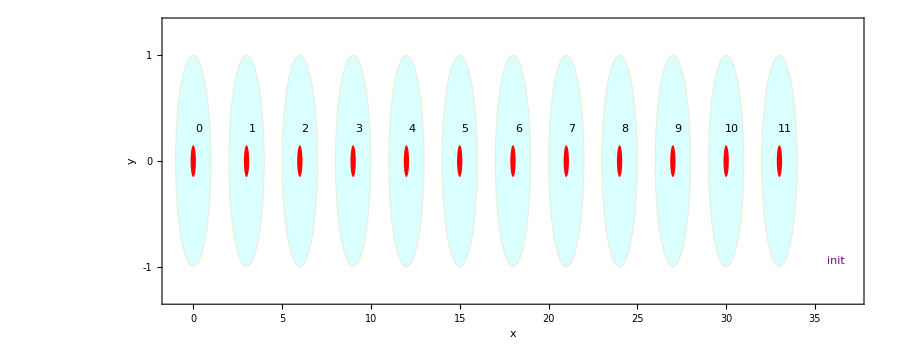

```mathematica
devGS=RydbergHub[];
showgs["init"]
```

```mathematica
circ1=CircRydbergHub[Flatten@{{Subscript[Init, #],Subscript[Ry, #][π/2]}&/@Range[0,11]},RydbergHub[],Parallel->True];
circ2={{Subscript[ShiftLoc, Range[1,11,2]][{-0.75,0}]}};
circ3={Subscript[C, #][Subscript[Z, #+1]]&/@Range[0,10,2]};
circ4={{Subscript[ShiftLoc, Range[1,11,2]][{1.5,0}]}};
circ5={Subscript[C, #][Subscript[Z, #+1]]&/@Range[1,9,2]};
```

```mathematica
devGS=RydbergHub[];
f1=showgs["initial",{ImagePadding->{{30,20},{0,0}}}];
noisycirc1=InsertCircuitNoise[circ1,devGS];
noisycirc2=InsertCircuitNoise[circ2,devGS];
f2=showgs["move 1",{ImagePadding->{{30,20},{0,0}}}];
noisycirc3=InsertCircuitNoise[circ3,devGS];
noisycirc4=InsertCircuitNoise[circ4,devGS];
f3=showgs["move 2",{ImagePadding->{{30,20},{20,0}}}];
noisycirc5=InsertCircuitNoise[circ5,devGS];
```

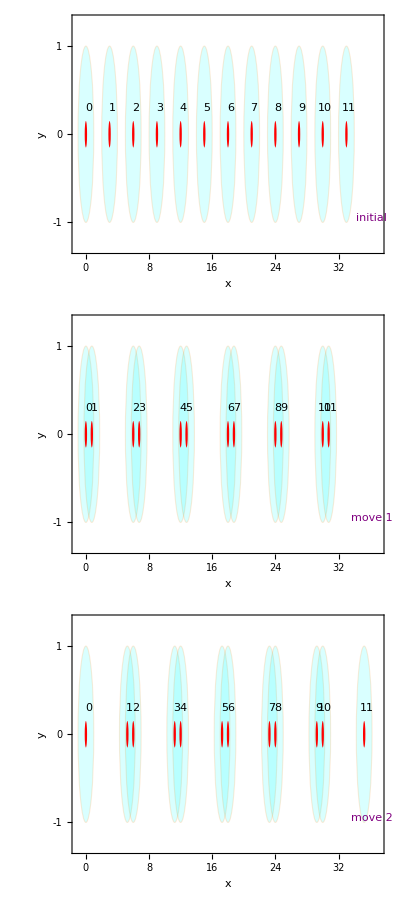

~/vqd/img/rydberg_graph.pdf

```mathematica
Column[{f1,f2,f3},Spacings->0]
Export["~/vqd/img/rydberg_graph.pdf",%]
```

Total  circuit excluding measurement

```mathematica
SetQuregMatrix[ρinit,RandomMixState[12]];
```

```mathematica
totalcirc=Join@@(ToExpression["circ"<>ToString@#]&/@Range[1,5])
```

{{Init_0,Init_1,Init_2,Init_3,Init_4,Init_5,Init_6,Init_7,Init_8,Init_9,Init_10,Init_11},{Ry_0[π/2],Ry_1[π/2],Ry_2[π/2],Ry_3[π/2],Ry_4[π/2],Ry_5[π/2],Ry_6[π/2],Ry_7[π/2],Ry_8[π/2],Ry_9[π/2],Ry_10[π/2],Ry_11[π/2]},{ShiftLoc_{1,3,5,7,9,11}[{-0.75,0}]},{C_0[Z_1],C_2[Z_3],C_4[Z_5],C_6[Z_7],C_8[Z_9],C_10[Z_11]},{ShiftLoc_{1,3,5,7,9,11}[{1.5,0}]},{C_1[Z_2],C_3[Z_4],C_5[Z_6],C_7[Z_8],C_9[Z_10]}}

```mathematica
noisycirc=InsertCircuitNoise[totalcirc,RydbergHub[]];
(*Simplify, remove errors with zero-parameters *)
enoisycirc=DeleteElements[ExtractCircuit[noisycirc],{Subscript[Depol, __][0.],Subscript[Deph, __][0.]}];
```

Run the circuit without measurement. We start from an unknown mixed state

```mathematica
ApplyCircuit[CloneQureg[ρ,ρinit],enoisycirc]
```

{}

Perfect measurement. Quoted value: 0.91. Noisy: 0.87

{0.91502,0.915066,0.915034,0.915069,0.915034,0.915069,0.915034,0.915069,0.915034,0.915069,0.915031,0.915059}

0.915049

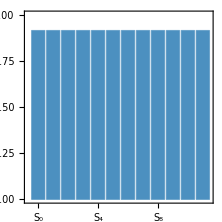

```mathematica
stabdata=CalcExpecPauliString[ρ,stabgs[g,#],ρwork]&/@Range[0,11]
Mean@stabdata
BarChart[stabdata,ChartLabels->(ToString[Subscript["S", #],TraditionalForm]&/@Range[0,11]),Frame->True,FrameStyle->Directive[Black,Thick],AspectRatio->1,ChartStyle->ColorData["Rainbow"][0.3],PlotRange->{Automatic,{0,1}}]
```

Gather the statistics by shots

Note that the “X” measurement done in the circuit is flipped: H=Ry[π/2]X

```mathematica
CalcCircuitMatrix[{Subscript[Ry, 0][π/2],Subscript[X, 0]}]//MatrixForm
```

(1/(√2) | 1/(√2)
1/(√2) | -1/(√2))

```mathematica
DrawCircuit@{Subscript[Ry, 0][π/2],Subscript[X, 0]}
```

-Graphics-

```mathematica
CalcCircuitMatrix[Subscript[X, 0]].CalcCircuitMatrix[Subscript[Ry, 0][π/2]]
```

{{1/(√2),1/(√2)},{1/(√2),-1/(√2)}}

```mathematica
Options[RydbergHub]={
qubitsNum-> 12,
AtomLocations->Association@Table[j->{j,0},{j,0,11}],
T2->1.5*10^6,
VacLifeTime->48*10^6,
RabiFreq->1,
ProbBFRot-><|10->0.01, 01->0.03|>,
ProbLeakMove->0.001,
UnitLattice->3,
BlockadeRadius->1,
ProbLeakInit->0.0001,
DurInit->5*10^5,
FidMeas-> 0.97,
DurMeas-> 10,
ProbLossMeas-> 0.01,
ProbLeakCZ-><|01->0.05,11->0.001|>
};
```

```mathematica
(*Two measurement settings: {Subscript[S, j]} where (1) j are even, (2) j are odd  
Put measurements at the very last!*)
evensm={Subscript[Ry, #][π/2]&/@Range[0,11,2],Subscript[M, #]&/@Range[0,11]};
oddsm={Subscript[Ry, #][π/2]&/@Range[1,11,2],Subscript[M, #]&/@Range[0,11]};
```

```mathematica
SimulateGraphState[ρ_,ρinit_,ρwork_,ρstore_,nshots_,options_:{}]:=Module[{noisycirc,enoisycirc,emeasnoisy,omeasnoisy,statevenmeas={},statoddmeas={},scount,outeig,stabideal,totalcirc},
totalcirc={{Subscript[Init, 0],Subscript[Init, 1],Subscript[Init, 2],Subscript[Init, 3],Subscript[Init, 4],Subscript[Init, 5],Subscript[Init, 6],Subscript[Init, 7],Subscript[Init, 8],Subscript[Init, 9],Subscript[Init, 10],Subscript[Init, 11]},{Subscript[Ry, 0][π/2],Subscript[Ry, 1][π/2],Subscript[Ry, 2][π/2],Subscript[Ry, 3][π/2],Subscript[Ry, 4][π/2],Subscript[Ry, 5][π/2],Subscript[Ry, 6][π/2],Subscript[Ry, 7][π/2],Subscript[Ry, 8][π/2],Subscript[Ry, 9][π/2],Subscript[Ry, 10][π/2],Subscript[Ry, 11][π/2]},{Subscript[ShiftLoc, {1,3,5,7,9,11}][{-0.75,0}]},{Subscript[C, 0][Subscript[Z, 1]],Subscript[C, 2][Subscript[Z, 3]],Subscript[C, 4][Subscript[Z, 5]],Subscript[C, 6][Subscript[Z, 7]],Subscript[C, 8][Subscript[Z, 9]],Subscript[C, 10][Subscript[Z, 11]]},{Subscript[ShiftLoc, {1,3,5,7,9,11}][{1.5,0}]},{Subscript[C, 1][Subscript[Z, 2]],Subscript[C, 3][Subscript[Z, 4]],Subscript[C, 5][Subscript[Z, 6]],Subscript[C, 7][Subscript[Z, 8]],Subscript[C, 9][Subscript[Z, 10]]}};
noisycirc=InsertCircuitNoise[totalcirc,RydbergHub[Sequence@@options]];
(*Simplify, remove errors with zero-parameters *)
     enoisycirc=DeleteElements[ExtractCircuit[noisycirc],{Subscript[Depol, __][0.],Subscript[Deph, __][0.]}];
ApplyCircuit[CloneQureg[ρ,ρinit],enoisycirc];
CloneQureg[ρstore,ρ];
emeasnoisy=ExtractCircuit@InsertCircuitNoise[evensm,RydbergHub[Sequence@@options]];
omeasnoisy=ExtractCircuit@InsertCircuitNoise[oddsm,RydbergHub[Sequence@@options]];

Table[
(* Note that this is okay because we don't have any function that depends on the absolute time.*)
(* even measurements*)
CloneQureg[ρ,ρstore];
AppendTo[statevenmeas,Flatten@ApplyCircuit[ρ,emeasnoisy]];
(* odd measurements*)
CloneQureg[ρ,ρstore];
AppendTo[statoddmeas,Flatten@ApplyCircuit[ρ,omeasnoisy]];
,{nshots}];
(* stabilizer count *)
scount=Association@Table[j->0,{j,VertexList@g}];
(* First measurement setting: X,Z,X,Z...*)
Table[
outeig=Table[
If[EvenQ[k-1],
out[[k]]/.{0:>-1},(*flip*)
out[[k]]/.{1:>-1,0:>1}
],{k,Length@out}];
Table[
(* +1 - -1 *)
scount[node]+=Times@@(outeig[[#+1]]&/@VertexList[NeighborhoodGraph[g,node]]);
,{node,0,11,2}];
,{out,statevenmeas}];

(* Second measurement setting: Z,X,Z,X...*)
Table[
outeig=Table[
If[OddQ[k-1],
out[[k]]/.{0:>-1}, (*flip*)
out[[k]]/.{1:>-1,0:>1}
],{k,Length@out}];
Table[
scount[node]+=Times@@(outeig[[#+1]]&/@VertexList[NeighborhoodGraph[g,node]]);
,{node,1,11,2}];
,{out,statoddmeas}];
stabideal=CalcExpecPauliString[CloneQureg[ρ,ρstore],stabgs[g,#],ρwork]&/@Range[0,11];
Print[options];
Print[Show[
BarChart[Values@scount/nshots,ChartLabels->(ToString[Subscript["S", #],TraditionalForm]&/@Range[0,11]),Frame->True,FrameStyle->Directive[Black,Thick],AspectRatio->1,ChartStyle->ColorData["Rainbow"][0.3],PlotRange->{Automatic,{0,1}}],
ListPlot[{stabideal,stabideal},Joined->{False,True},PlotStyle->{Red,Black}],ImageSize->200
]," noisy<Sj>=",N@Mean@Values[scount/nshots],"  ideal<Sj>=",Mean[stabideal]];
<|"opt"->options,"outeven"->statevenmeas,"outodd"->statoddmeas,"scount"->scount,"sideal"->stabideal|>
]
```

```mathematica
DestroyAllQuregs[];
{ρ,ρinit,ρwork,ρstore}=CreateDensityQuregs[12,4];
```

```mathematica
SetQuregMatrix[ρinit,RandomMixState[12]];
```

```mathematica
fbrot=Flatten@Table[<|10->i,01->j|>,{i,{0.01,0.02}},{j,{0.02,0.03}}];
probleakinit={0.001,0.01};
probleakcz=Flatten@Table[<|10->i,11->j|>,{i,{0.01,0.05}},{j,{0.005,0.001}}];
fidmeas={0.97,0.98,0.98,0.99};
```

```mathematica
options=Flatten[Table[{ProbBFRot->i,ProbLeakInit->j,ProbLeakCZ->k,FidMeas->l},{i,fbrot},{j,probleakinit},{k,probleakcz},{l,fidmeas}],3];
```

{ProbBFRot→<|10→0.01,1→0.02|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.97}

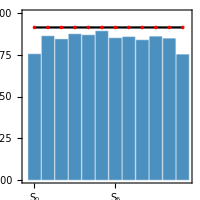
-Graphics- noisy<Sj>=0.84125  ideal<Sj>=0.924356

{ProbBFRot→<|10→0.01,1→0.02|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.98}

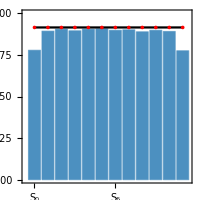
-Graphics- noisy<Sj>=0.877917  ideal<Sj>=0.924356

{ProbBFRot→<|10→0.01,1→0.02|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.98}

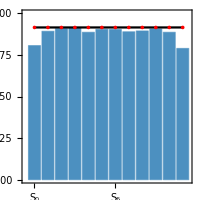
-Graphics- noisy<Sj>=0.881333  ideal<Sj>=0.924356

{ProbBFRot→<|10→0.01,1→0.02|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.99}

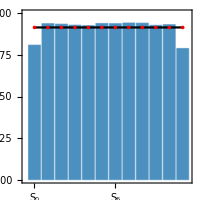
-Graphics- noisy<Sj>=0.912167  ideal<Sj>=0.924356

{ProbBFRot→<|10→0.01,1→0.02|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.97}

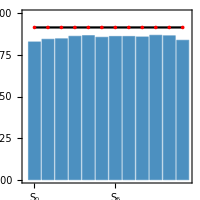
-Graphics- noisy<Sj>=0.8545  ideal<Sj>=0.966319

{ProbBFRot→<|10→0.01,1→0.02|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.98}

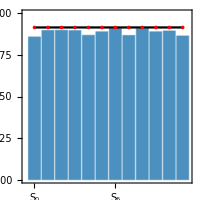
-Graphics- noisy<Sj>=0.8865  ideal<Sj>=0.966319

{ProbBFRot→<|10→0.01,1→0.02|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.98}

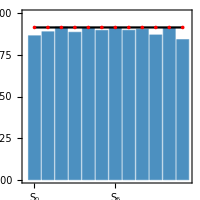
-Graphics- noisy<Sj>=0.89225  ideal<Sj>=0.966319

{ProbBFRot→<|10→0.01,1→0.02|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.99}

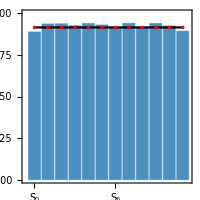
-Graphics- noisy<Sj>=0.923667  ideal<Sj>=0.966319

{ProbBFRot→<|10→0.01,1→0.02|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.97}

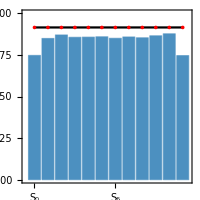
-Graphics- noisy<Sj>=0.840583  ideal<Sj>=0.924356

{ProbBFRot→<|10→0.01,1→0.02|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.98}

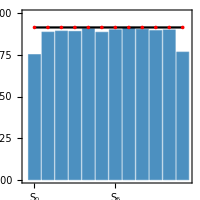
-Graphics- noisy<Sj>=0.874917  ideal<Sj>=0.924356

{ProbBFRot→<|10→0.01,1→0.02|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.98}

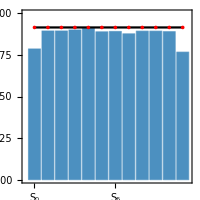
-Graphics- noisy<Sj>=0.873667  ideal<Sj>=0.924356

{ProbBFRot→<|10→0.01,1→0.02|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.99}

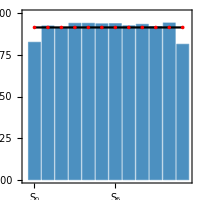
-Graphics- noisy<Sj>=0.912917  ideal<Sj>=0.924356

{ProbBFRot→<|10→0.01,1→0.02|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.97}

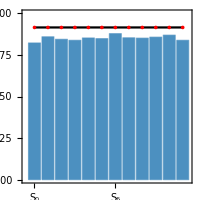
-Graphics- noisy<Sj>=0.85075  ideal<Sj>=0.966319

{ProbBFRot→<|10→0.01,1→0.02|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.98}

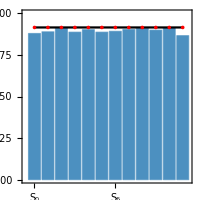
-Graphics- noisy<Sj>=0.894833  ideal<Sj>=0.966319

{ProbBFRot→<|10→0.01,1→0.02|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.98}

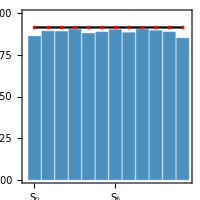
-Graphics- noisy<Sj>=0.886  ideal<Sj>=0.966319

{ProbBFRot→<|10→0.01,1→0.02|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.99}

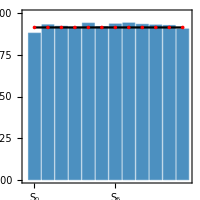
-Graphics- noisy<Sj>=0.923833  ideal<Sj>=0.966319

{ProbBFRot→<|10→0.01,1→0.02|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.97}

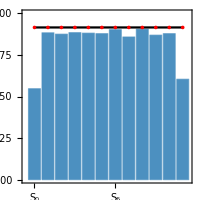
-Graphics- noisy<Sj>=0.830333  ideal<Sj>=0.829232

{ProbBFRot→<|10→0.01,1→0.02|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.98}

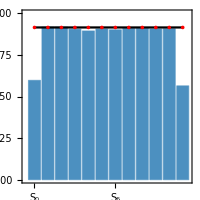
-Graphics- noisy<Sj>=0.85275  ideal<Sj>=0.829232

{ProbBFRot→<|10→0.01,1→0.02|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.98}

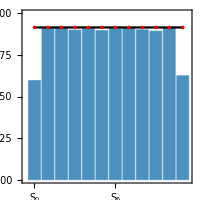
-Graphics- noisy<Sj>=0.85675  ideal<Sj>=0.829232

{ProbBFRot→<|10→0.01,1→0.02|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.99}

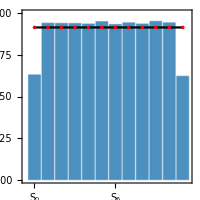
-Graphics- noisy<Sj>=0.88875  ideal<Sj>=0.829232

{ProbBFRot→<|10→0.01,1→0.02|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.97}

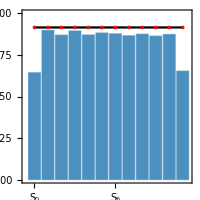
-Graphics- noisy<Sj>=0.8385  ideal<Sj>=0.866876

{ProbBFRot→<|10→0.01,1→0.02|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.98}

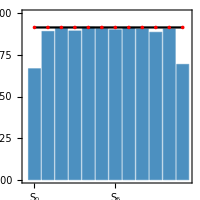
-Graphics- noisy<Sj>=0.866  ideal<Sj>=0.866876

{ProbBFRot→<|10→0.01,1→0.02|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.98}

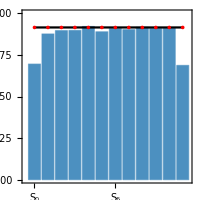
-Graphics- noisy<Sj>=0.867167  ideal<Sj>=0.866876

{ProbBFRot→<|10→0.01,1→0.02|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.99}

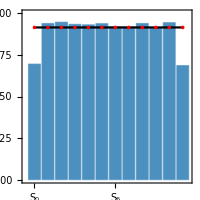
-Graphics- noisy<Sj>=0.891833  ideal<Sj>=0.866876

{ProbBFRot→<|10→0.01,1→0.02|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.97}

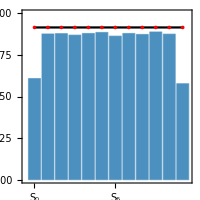
-Graphics- noisy<Sj>=0.829167  ideal<Sj>=0.829232

{ProbBFRot→<|10→0.01,1→0.02|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.98}

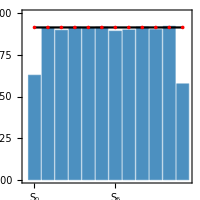
-Graphics- noisy<Sj>=0.858083  ideal<Sj>=0.829232

{ProbBFRot→<|10→0.01,1→0.02|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.98}

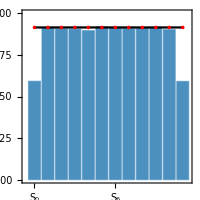
-Graphics- noisy<Sj>=0.856167  ideal<Sj>=0.829232

{ProbBFRot→<|10→0.01,1→0.02|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.99}

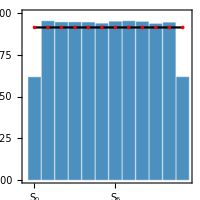
-Graphics- noisy<Sj>=0.890167  ideal<Sj>=0.829232

{ProbBFRot→<|10→0.01,1→0.02|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.97}

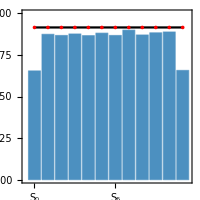
-Graphics- noisy<Sj>=0.840167  ideal<Sj>=0.866876

{ProbBFRot→<|10→0.01,1→0.02|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.98}

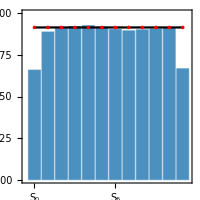
-Graphics- noisy<Sj>=0.867  ideal<Sj>=0.866876

{ProbBFRot→<|10→0.01,1→0.02|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.98}

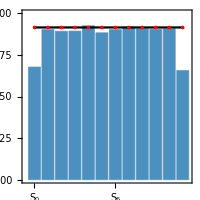
-Graphics- noisy<Sj>=0.863667  ideal<Sj>=0.866876

{ProbBFRot→<|10→0.01,1→0.02|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.99}

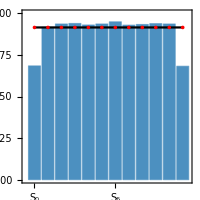
-Graphics- noisy<Sj>=0.892333  ideal<Sj>=0.866876

{ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.97}

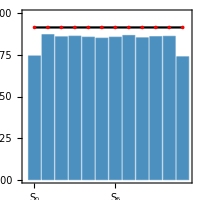
-Graphics- noisy<Sj>=0.840333  ideal<Sj>=0.919118

{ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.98}

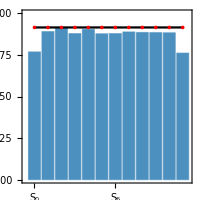
-Graphics- noisy<Sj>=0.867333  ideal<Sj>=0.919118

{ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.98}

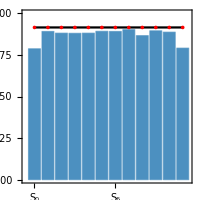
-Graphics- noisy<Sj>=0.870333  ideal<Sj>=0.919118

{ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.99}

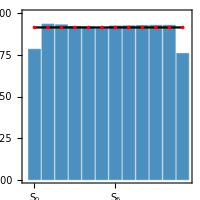
-Graphics- noisy<Sj>=0.899083  ideal<Sj>=0.919118

{ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.97}

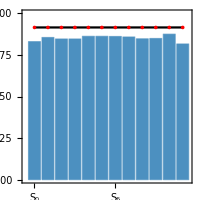
-Graphics- noisy<Sj>=0.850583  ideal<Sj>=0.961228

{ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.98}

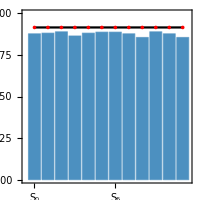
-Graphics- noisy<Sj>=0.876583  ideal<Sj>=0.961228

{ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.98}

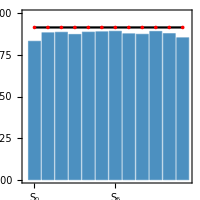
-Graphics- noisy<Sj>=0.87625  ideal<Sj>=0.961228

{ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.99}

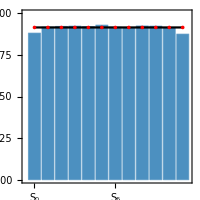
-Graphics- noisy<Sj>=0.912917  ideal<Sj>=0.961228

{ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.97}

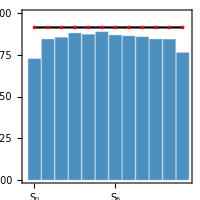
-Graphics- noisy<Sj>=0.840917  ideal<Sj>=0.919118

{ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.98}

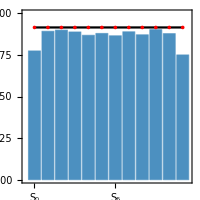
-Graphics- noisy<Sj>=0.862917  ideal<Sj>=0.919118

{ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.98}

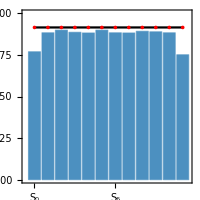
-Graphics- noisy<Sj>=0.8665  ideal<Sj>=0.919118

{ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.99}

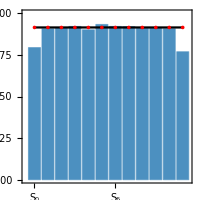
-Graphics- noisy<Sj>=0.892667  ideal<Sj>=0.919118

{ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.97}

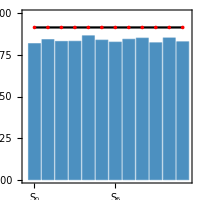
-Graphics- noisy<Sj>=0.83775  ideal<Sj>=0.961228

{ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.98}

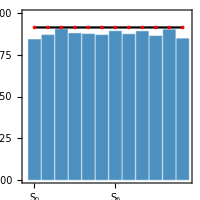
-Graphics- noisy<Sj>=0.8755  ideal<Sj>=0.961228

{ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.98}

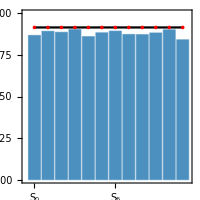
-Graphics- noisy<Sj>=0.879333  ideal<Sj>=0.961228

{ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.99}

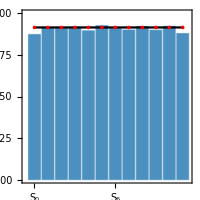
-Graphics- noisy<Sj>=0.905333  ideal<Sj>=0.961228

{ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.97}

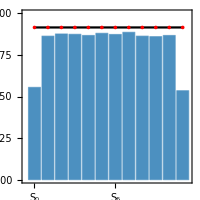
-Graphics- noisy<Sj>=0.816583  ideal<Sj>=0.824532

{ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.98}

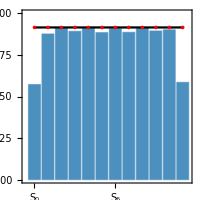
-Graphics- noisy<Sj>=0.844667  ideal<Sj>=0.824532

{ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.98}

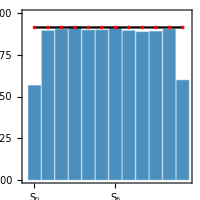
-Graphics- noisy<Sj>=0.846667  ideal<Sj>=0.824532

{ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.99}

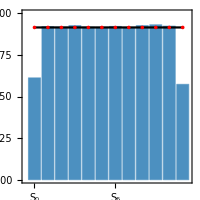
-Graphics- noisy<Sj>=0.866417  ideal<Sj>=0.824532

{ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.97}

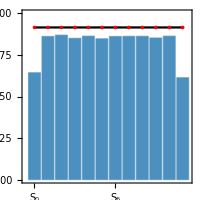
-Graphics- noisy<Sj>=0.8205  ideal<Sj>=0.862309

{ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.98}

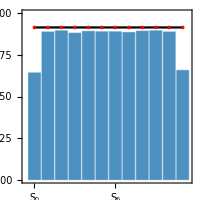
-Graphics- noisy<Sj>=0.8495  ideal<Sj>=0.862309

{ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.98}

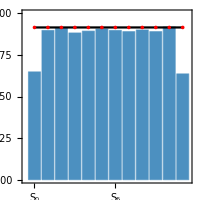
-Graphics- noisy<Sj>=0.855667  ideal<Sj>=0.862309

{ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.99}

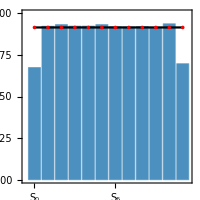
-Graphics- noisy<Sj>=0.884417  ideal<Sj>=0.862309

{ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.97}

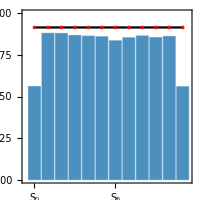
-Graphics- noisy<Sj>=0.811167  ideal<Sj>=0.824532

{ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.98}

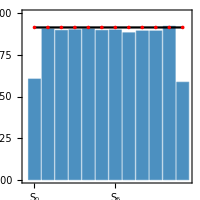
-Graphics- noisy<Sj>=0.84925  ideal<Sj>=0.824532

{ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.98}

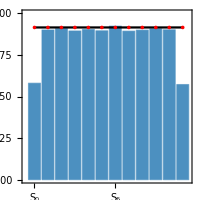
-Graphics- noisy<Sj>=0.847917  ideal<Sj>=0.824532

{ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.99}

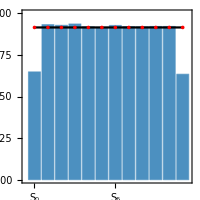
-Graphics- noisy<Sj>=0.87675  ideal<Sj>=0.824532

{ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.97}

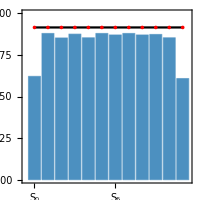
-Graphics- noisy<Sj>=0.826  ideal<Sj>=0.862309

{ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.98}

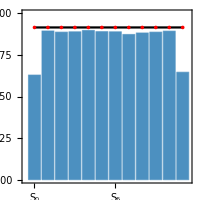
-Graphics- noisy<Sj>=0.846333  ideal<Sj>=0.862309

{ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.98}

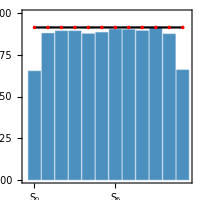
-Graphics- noisy<Sj>=0.852083  ideal<Sj>=0.862309

{ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.99}

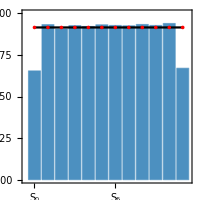
-Graphics- noisy<Sj>=0.882583  ideal<Sj>=0.862309

{ProbBFRot→<|10→0.02,1→0.02|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.97}

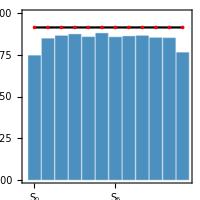
-Graphics- noisy<Sj>=0.842667  ideal<Sj>=0.929576

{ProbBFRot→<|10→0.02,1→0.02|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.98}

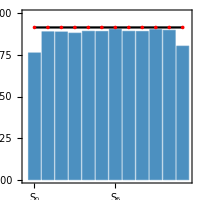
-Graphics- noisy<Sj>=0.874417  ideal<Sj>=0.929576

{ProbBFRot→<|10→0.02,1→0.02|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.98}

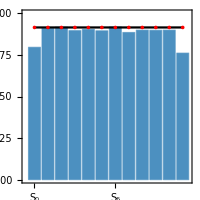
-Graphics- noisy<Sj>=0.8815  ideal<Sj>=0.929576

{ProbBFRot→<|10→0.02,1→0.02|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.99}

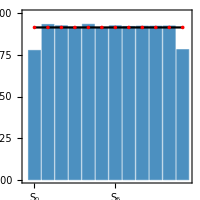
-Graphics- noisy<Sj>=0.89975  ideal<Sj>=0.929576

{ProbBFRot→<|10→0.02,1→0.02|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.97}

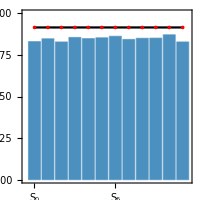
-Graphics- noisy<Sj>=0.847167  ideal<Sj>=0.971387

{ProbBFRot→<|10→0.02,1→0.02|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.98}

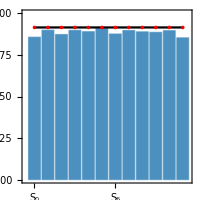
-Graphics- noisy<Sj>=0.885333  ideal<Sj>=0.971387

{ProbBFRot→<|10→0.02,1→0.02|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.98}

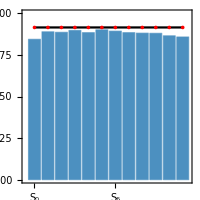
-Graphics- noisy<Sj>=0.880167  ideal<Sj>=0.971387

{ProbBFRot→<|10→0.02,1→0.02|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.99}

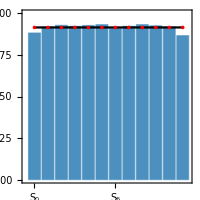
-Graphics- noisy<Sj>=0.915167  ideal<Sj>=0.971387

{ProbBFRot→<|10→0.02,1→0.02|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.97}

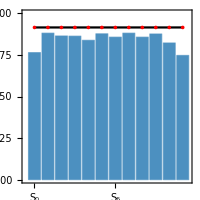
-Graphics- noisy<Sj>=0.843917  ideal<Sj>=0.929576

{ProbBFRot→<|10→0.02,1→0.02|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.98}

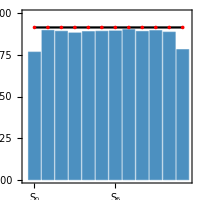
-Graphics- noisy<Sj>=0.872667  ideal<Sj>=0.929576

{ProbBFRot→<|10→0.02,1→0.02|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.98}

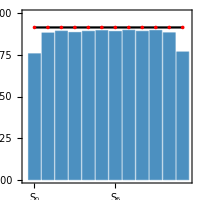
-Graphics- noisy<Sj>=0.8695  ideal<Sj>=0.929576

{ProbBFRot→<|10→0.02,1→0.02|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.99}

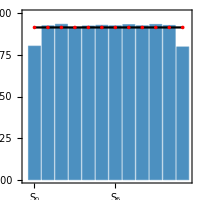
-Graphics- noisy<Sj>=0.905667  ideal<Sj>=0.929576

{ProbBFRot→<|10→0.02,1→0.02|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.97}

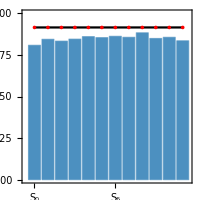
-Graphics- noisy<Sj>=0.84875  ideal<Sj>=0.971387

{ProbBFRot→<|10→0.02,1→0.02|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.98}

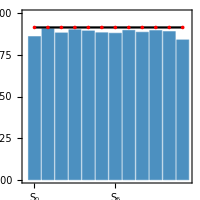
-Graphics- noisy<Sj>=0.884667  ideal<Sj>=0.971387

{ProbBFRot→<|10→0.02,1→0.02|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.98}

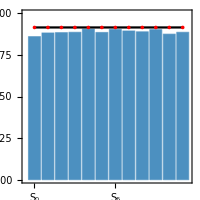
-Graphics- noisy<Sj>=0.887583  ideal<Sj>=0.971387

{ProbBFRot→<|10→0.02,1→0.02|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.99}

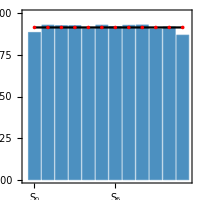
-Graphics- noisy<Sj>=0.9145  ideal<Sj>=0.971387

{ProbBFRot→<|10→0.02,1→0.02|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.97}

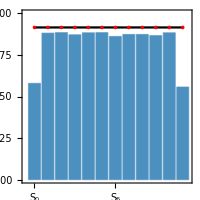
-Graphics- noisy<Sj>=0.824583  ideal<Sj>=0.833914

{ProbBFRot→<|10→0.02,1→0.02|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.98}

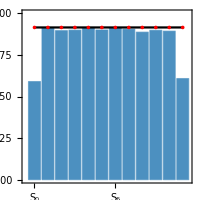
-Graphics- noisy<Sj>=0.851417  ideal<Sj>=0.833914

{ProbBFRot→<|10→0.02,1→0.02|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.98}

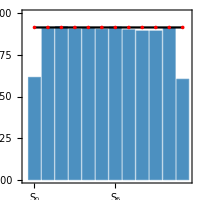
-Graphics- noisy<Sj>=0.8575  ideal<Sj>=0.833914

{ProbBFRot→<|10→0.02,1→0.02|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.99}

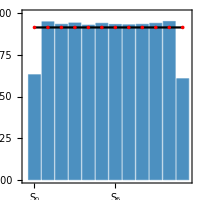
-Graphics- noisy<Sj>=0.885083  ideal<Sj>=0.833914

{ProbBFRot→<|10→0.02,1→0.02|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.97}

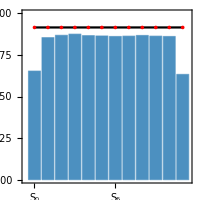
-Graphics- noisy<Sj>=0.827333  ideal<Sj>=0.871422

{ProbBFRot→<|10→0.02,1→0.02|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.98}

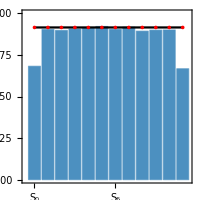
-Graphics- noisy<Sj>=0.867  ideal<Sj>=0.871422

{ProbBFRot→<|10→0.02,1→0.02|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.98}

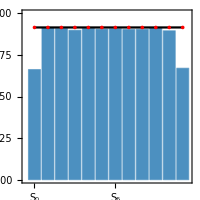
-Graphics- noisy<Sj>=0.865333  ideal<Sj>=0.871422

{ProbBFRot→<|10→0.02,1→0.02|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.99}

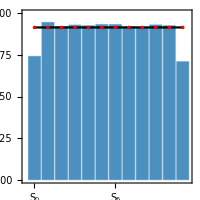
-Graphics- noisy<Sj>=0.893583  ideal<Sj>=0.871422

{ProbBFRot→<|10→0.02,1→0.02|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.97}

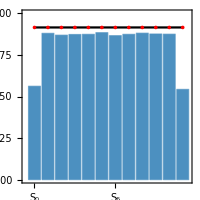
-Graphics- noisy<Sj>=0.821417  ideal<Sj>=0.833914

{ProbBFRot→<|10→0.02,1→0.02|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.98}

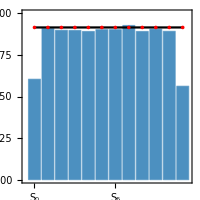
-Graphics- noisy<Sj>=0.84825  ideal<Sj>=0.833914

{ProbBFRot→<|10→0.02,1→0.02|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.98}

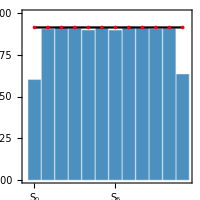
-Graphics- noisy<Sj>=0.858333  ideal<Sj>=0.833914

{ProbBFRot→<|10→0.02,1→0.02|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.99}

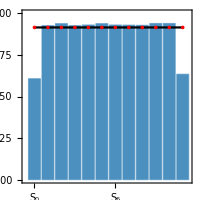
-Graphics- noisy<Sj>=0.880333  ideal<Sj>=0.833914

{ProbBFRot→<|10→0.02,1→0.02|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.97}

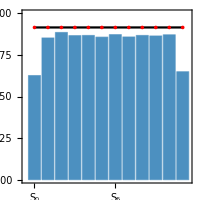
-Graphics- noisy<Sj>=0.827833  ideal<Sj>=0.871422

{ProbBFRot→<|10→0.02,1→0.02|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.98}

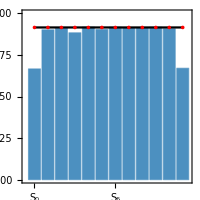
-Graphics- noisy<Sj>=0.867917  ideal<Sj>=0.871422

{ProbBFRot→<|10→0.02,1→0.02|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.98}

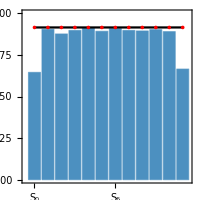
-Graphics- noisy<Sj>=0.85675  ideal<Sj>=0.871422

{ProbBFRot→<|10→0.02,1→0.02|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.99}

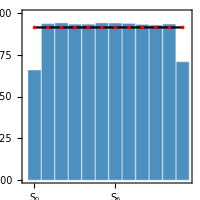
-Graphics- noisy<Sj>=0.891583  ideal<Sj>=0.871422

{ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.97}

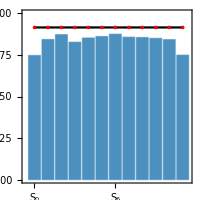
-Graphics- noisy<Sj>=0.835833  ideal<Sj>=0.924313

{ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.98}

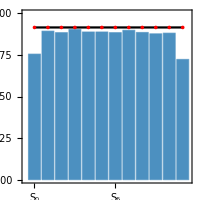
-Graphics- noisy<Sj>=0.86325  ideal<Sj>=0.924313

$Aborted

```mathematica
outputsgs=SimulateGraphState[ρ,ρinit,ρwork,ρstore,2000,#]&/@options;
```

```mathematica
bfrot={0.02,0.03};
fidmeas={0.96,0.97,0.98};
options=Flatten[Table[{ProbBFRot-><|10->0.01,01->i|>,FidMeas->j},{i,bfrot},{j,fidmeas}],1]
```

{{ProbBFRot→<|10→0.01,1→0.02|>,FidMeas→0.96},{ProbBFRot→<|10→0.01,1→0.02|>,FidMeas→0.97},{ProbBFRot→<|10→0.01,1→0.02|>,FidMeas→0.98},{ProbBFRot→<|10→0.01,1→0.03|>,FidMeas→0.96},{ProbBFRot→<|10→0.01,1→0.03|>,FidMeas→0.97},{ProbBFRot→<|10→0.01,1→0.03|>,FidMeas→0.98}}

{ProbBFRot→<|10→0.01,1→0.02|>,FidMeas→0.96}

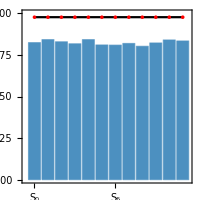
-Graphics- noisy<Sj>=0.824167  ideal<Sj>=0.976818

{ProbBFRot→<|10→0.01,1→0.02|>,FidMeas→0.97}

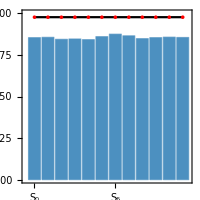
-Graphics- noisy<Sj>=0.854667  ideal<Sj>=0.976818

{ProbBFRot→<|10→0.01,1→0.02|>,FidMeas→0.98}

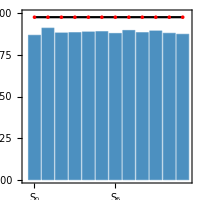
-Graphics- noisy<Sj>=0.885917  ideal<Sj>=0.976818

{ProbBFRot→<|10→0.01,1→0.03|>,FidMeas→0.96}

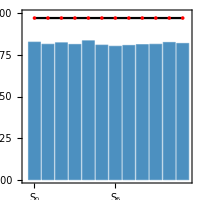
-Graphics- noisy<Sj>=0.816667  ideal<Sj>=0.971671

{ProbBFRot→<|10→0.01,1→0.03|>,FidMeas→0.97}

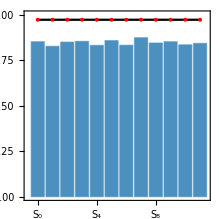
-Graphics- noisy<Sj>=0.84525  ideal<Sj>=0.971671

{ProbBFRot→<|10→0.01,1→0.03|>,FidMeas→0.98}

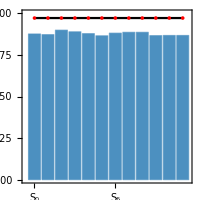
-Graphics- noisy<Sj>=0.877667  ideal<Sj>=0.971671

```mathematica
outputsgs=Table[SimulateGraphState[ρ,ρinit,ρwork,ρstore,2000,op],{op,options}];
```

```mathematica
opt={ProbBFRot-><|10->0.01,1->0.03|>,FidMeas->0.97}
```

{ProbBFRot→<|10→0.01,1→0.03|>,FidMeas→0.97}

```mathematica
Options@RydbergHub
```

{qubitsNum→12,AtomLocations→<|0→{0,0},1→{1,0},2→{2,0},3→{3,0},4→{4,0},5→{5,0},6→{6,0},7→{7,0},8→{8,0},9→{9,0},10→{10,0},11→{11,0}|>,T2→1.5×10^6,VacLifeTime→48000000,RabiFreq→1,ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakMove→0.001,UnitLattice→3,BlockadeRadius→1,ProbLeakInit→0.0001,DurInit→500000,FidMeas→0.97,DurMeas→10,ProbLossMeas→0.01,ProbLeakCZ→<|1→0.05,11→0.001|>}

{FidMeas→0.975}

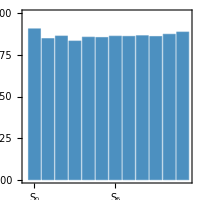
-Graphics- noisy<Sj>=0.8645  ideal<Sj>=3979.97

{FidMeas→0.975}

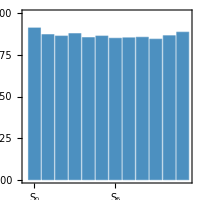
-Graphics- noisy<Sj>=0.8665  ideal<Sj>=3979.97

```mathematica
mainres=Table[
SetQuregMatrix[ρinit,IdentityMatrix[2^12]];
SimulateGraphState[ρ,ρinit,ρwork,ρstore,3000,{FidMeas->0.975}],{2}];
```

{}

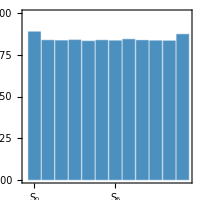
-Graphics- noisy<Sj>=0.843983  ideal<Sj>=3979.97

```mathematica
SetQuregMatrix[ρinit,IdentityMatrix[2^12]];
mainres2=SimulateGraphState[ρ,ρinit,ρwork,ρstore,10000];
```

```mathematica
mainres3=SimulateGraphState[ρ,ρinit,ρwork,ρstore,10000,{FidMeas->0.977}];
```

{FidMeas→0.977}

-Graphics- noisy<Sj>=0.872717  ideal<Sj>=3979.97

```mathematica
mainres3//Keys
```

{opt,outeven,outodd,scount,sideal}

```mathematica
gsresults3k=Table[
SetQuregMatrix[ρinit,IdentityMatrix[2^12]];
SimulateGraphState[ρ,ρinit,ρwork,ρstore,3000],{2}];
```

{}

-Graphics- noisy<Sj>=0.846778  ideal<Sj>=3979.97

{}

-Graphics- noisy<Sj>=0.852056  ideal<Sj>=3979.97

```mathematica
(* do 10 experiments with random initial state for 2000 shots on each measurement *)
outputsgs=Table[
SetQuregMatrix[ρinit,RandomMixState[12]];
SimulateGraphState[ρ,ρinit,ρwork,ρstore,2000],{10}];
```

{}

-Graphics- noisy<Sj>=0.838417  ideal<Sj>=0.971671

{}

-Graphics- noisy<Sj>=0.83975  ideal<Sj>=0.971671

{}

-Graphics- noisy<Sj>=0.84375  ideal<Sj>=0.971671

{}

-Graphics- noisy<Sj>=0.848333  ideal<Sj>=0.971671

{}

-Graphics- noisy<Sj>=0.837833  ideal<Sj>=0.971671

{}

-Graphics- noisy<Sj>=0.847167  ideal<Sj>=0.971671

{}

-Graphics- noisy<Sj>=0.839833  ideal<Sj>=0.971671

{}

-Graphics- noisy<Sj>=0.846667  ideal<Sj>=0.971671

{}

-Graphics- noisy<Sj>=0.8445  ideal<Sj>=0.971671

{}

-Graphics- noisy<Sj>=0.839917  ideal<Sj>=0.971671

```mathematica
Mean@gsresults1k[[All,"scount"]]/1000
```

<|0→523/625,1→531/625,2→2097/2500,3→1049/1250,4→527/625,5→4221/5000,6→526/625,7→1057/1250,8→4253/5000,9→1051/1250,10→2133/2500,11→4231/5000|>

```mathematica
mainres3<<mainres3.mx
```

```mathematica
mainres3//Keys
```

{opt,outeven,outodd,scount,sideal}

```mathematica
nshots=10000;
mainres3["scount"]
mainres3["sideal"]/2^12
```

<|0→9122,1→8658,2→8786,3→8632,4→8732,5→8676,6→8534,7→8656,8→8644,9→8678,10→8692,11→8916|>

{0.971646,0.971681,0.971666,0.971684,0.971666,0.971684,0.971666,0.971684,0.971666,0.971684,0.971663,0.971664}

```mathematica
Show[
BarChart[Values@mainres3["scount"]/nshots,ChartLabels->(ToString[Subscript["S", #],TraditionalForm]&/@Range[0,11]),Frame->True,FrameStyle->Directive[Black,Thick],AspectRatio->1.5,ChartStyle->ColorData["Aquamarine"][0.7],PlotRange->{Automatic,{0,1}},FrameLabel->{"Stabiliser","Stabiliser expected value"},BaseStyle->{16,FontFamily->"Serif"}],
ListPlot[ConstantArray[mainres3["sideal"]/2^12,2],Joined->{True,False},PlotMarkers->{Black,7}],ImageSize->380

]
```

-Graphics-

```mathematica
Subscript[ColorData["Aquamarine"][#/10], #]&/@Range[10]
```

{RGBColor[0.7377701000000001, 0.7828292, 0.8663791]_1,RGBColor[0.7525574, 0.8025466, 0.863719]_2,RGBColor[0.7296247, 0.7974909, 0.844407]_3,RGBColor[0.6706896, 0.7677752, 0.810842]_4,RGBColor[0.604616, 0.7313985000000001, 0.7773175]_5,RGBColor[0.5419766, 0.6952484, 0.7485926]_6,RGBColor[0.4950612, 0.6663258, 0.7318262000000001]_7,RGBColor[0.494452, 0.662743, 0.7437104]_8,RGBColor[0.5384311, 0.6843868, 0.7818455]_9,RGBColor[0.631571, 0.734035, 0.848615]_10}

!!!The selected configuration and results: mainres3, with 10k shots of readout

## Steane code

```mathematica
stlocs=<|6->{0,1},5->{1,1},2->{2,1},1->{4,1},4->{2,0},0->{4,0},3->{5,0}|>;

Options[RydbergHub]={
qubitsNum-> 7,
AtomLocations->stlocs,
T2->1.5*10^6,
VacLifeTime->48*10^6,
RabiFreq->1,
ProbBFRot-><|10->0.01, 01->0.03|>,
ProbLeakMove->0.001,
UnitLattice->3,
BlockadeRadius->1,
ProbLeakInit->0.0001,
DurInit->5*10^5,
FidMeas-> 0.977,
DurMeas-> 10,
ProbLossMeas-> 0.01,
ProbLeakCZ-><|01->0.05,11->0.001|>
};
```

```mathematica
devst=RydbergHub[];
```

```mathematica
ClearAll[showst]
showst[title_:"",opt_:{}]:=PlotAtoms[devst,Sequence@@opt,ImageSize->600,ShowBlockade->Range[0,6],LabelStyle->Directive[Italic, 15,Black],BaseStyle->{17,FontFamily->"Serif"},PlotRange->{{-8,16},{-1.3,4.3}},Epilog->Inset[Style[title,{Purple,Italic}],Scaled[{0.2,0.1}]],Frame->True,FrameStyle->Directive[Black,Thick],Axes->False];
```

```mathematica
move0=showst["initial",{ImagePadding->{{20,18},{0,18}}}]
```

-Graphics-

```mathematica
devst=RydbergHub[];
circ0={Subscript[Init, #]&/@Range[0,6],Subscript[Ry, #][π/2]&/@Range[0,6]};
circ1={{Subscript[ShiftLoc, 4,0,3][{-0.2,0.8}]},{Subscript[C, 2][Subscript[Z, 4]],Subscript[C, 0][Subscript[Z, 1]]}};
circ2={{Subscript[ShiftLoc, 2][{1,0}],Subscript[ShiftLoc, 4,0,3][{-1,0}]},{Subscript[C, 4][Subscript[Z, 5]],Subscript[C, 2][Subscript[Z, 0]],Subscript[C, 1][Subscript[Z, 3]]}};
circ3={{Subscript[ShiftLoc, 4,0,3][{-1,0}]},{Subscript[C, 4][Subscript[Z, 6]],Subscript[C, 2][Subscript[Z, 3]]}};
circ4={{Subscript[ShiftLoc, 4,0,3][{-2,0}]},{Subscript[C, 0][Subscript[Z, 6]],Subscript[C, 3][Subscript[Z, 5]]},Subscript[Ry, #][π/2]&/@{0,3,4}};
circ5={{Subscript[ShiftLoc, 4,0,3][{-2,0}]},{Subscript[C, 0][Subscript[Z, 6]],Subscript[C, 3][Subscript[Z, 5]]},Subscript[Ry, #][π/2]&/@{1,2,5,6}};
InsertCircuitNoise[circ1,devst];
move1=showst["move 1",{ImagePadding->{{20,18},{0,0}},PlotRange->{{-8,16},{0.3,4.3}}}]
InsertCircuitNoise[circ2,devst];
move2=showst["move 2",{ImagePadding->{{20,18},{0,0}},PlotRange->{{-8,16},{0.3,4.3}}}]
InsertCircuitNoise[circ3,devst];
move3=showst["move 3",{ImagePadding->{{20,18},{0,0}},PlotRange->{{-8,16},{0.3,4.3}}}]
InsertCircuitNoise[circ4,devst];
move4=showst["move 4",{ImagePadding->{{20,18},{18,0}},PlotRange->{{-8,16},{0.3,4.3}}}]
```

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

```mathematica
Column[{move0,move1,move2,move3,move4},Spacings->-0.1]
Export["/home/cica/vqd/img/rydberg_steane.pdf",%]
```

-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-

/home/cica/vqd/img/rydberg_steane.pdf

Entire simulation

```mathematica
stabx={Subscript[X, 0] Subscript[X, 1] Subscript[X, 2] Subscript[X, 6],Subscript[X, 2] Subscript[X, 4] Subscript[X, 5] Subscript[X, 6],Subscript[X, 1] Subscript[X, 2] Subscript[X, 3] Subscript[X, 5]};
stabz={Subscript[Z, 0] Subscript[Z, 1] Subscript[Z, 2] Subscript[Z, 6],Subscript[Z, 2] Subscript[Z, 4] Subscript[Z, 5] Subscript[Z, 6],Subscript[Z, 1] Subscript[Z, 2] Subscript[Z, 3] Subscript[Z, 5]};
xlogic=Subscript[X, 0] Subscript[X, 1] Subscript[X, 3];
zlogic=Subscript[Z, 0] Subscript[Z, 1] Subscript[Z, 3];
(* returns indices of the involved stabilizers *)
stabindex[stab_]:=Level[stab,1]/.Subscript[_,j_]:>j
```

```mathematica
DestroyAllQuregs[]
{ρ,ρinit,ρwork}=CreateDensityQuregs[7,3];
```

```mathematica
noisycirc=InsertCircuitNoise[Join[circ0,circ1,circ2,circ3,circ4],RydbergHub[]];
(*simplify, and remove zero-parameterised operations *)
simpncirc=DeleteElements[ExtractCircuit[noisycirc],{Subscript[Depol, __][0.],Subscript[Deph, __][0.],Subscript[Damp, __][0.]}];
```

Logical |+>

```mathematica
DrawCircuit@DeleteElements[Flatten@Join[circ0,circ1,circ2,circ3,circ4],{Subscript[ShiftLoc, __][_]}]
```

-Graphics-

```mathematica
ApplyCircuit[SetQuregMatrix[ρ,IdentityMatrix[2^7]/2^7],simpncirc]
```

{}

```mathematica
(*list of some graph layouts*)
gl={"Automatic","CircularEmbedding","RandomEmbedding","SpiralEmbedding","GridEmbedding","SpringElectricalEmbedding","SpringEmbedding","HighDimensionalEmbedding","LayeredEmbedding","MultipartiteEmbedding","LayeredDigraphEmbedding","LayeredDrawing","RadialEmbedding","BipartiteEmbedding","BalloonEmbedding","TutteEmbedding","PlanarEmbedding","KamadaKawaiEmbedding","DavidsonHarelEmbedding"};
```

```mathematica
Graph[{2<->4,0<->1,4<->5,2<->0,1<->3,4<->6,2<->3,0<->6,3<->5},
VertexSize->0.5,VertexStyle->Directive[White,EdgeForm[Thick]],BaseStyle->{19,FontFamily->"Serif"},ImageSize->200,EdgeStyle->Directive[Black,Thick],VertexLabels->Placed[Automatic,Center],GraphLayout->"TutteEmbedding"]
Export["~/vqd/img/graphsteane.pdf",%]
```

-Graphics-

~/vqd/img/graphsteane.pdf

Ideal expected value of the stabilizers

```mathematica
sx=CalcExpecPauliString[ρ,#,ρwork]&/@stabx
sz=Table[
hidx={0,3,4};
zidx=stabindex[s];
sign=If[EvenQ[Length[Intersection[hidx,zidx]]],+1,-1];
sign*CalcExpecPauliString[ρ,s,ρwork],
{s,stabz}]
```

{0.944198,0.944192,0.944199}

{0.934903,0.934903,0.934906}

```mathematica
BarChart[Flatten@{sx,sz},ChartLabels->Join[(ToString[Subscript["X", #],TraditionalForm]&/@Range[0,2]),(ToString[Subscript["Z", #],TraditionalForm]&/@Range[0,2])],Frame->True,FrameStyle->Directive[Black,Thick],AspectRatio->1,ChartStyle->Join[ConstantArray[ColorData["AlpineColors"][0.1],3],ConstantArray[ColorData["AlpineColors"][0.9],3]]]
```

-Graphics-

Simulate the stabilizer measurements

```mathematica
stabindex@#&/@stabx
```

{{0,1,2,6},{2,4,5,6},{1,2,3,5}}

```mathematica
stabindex@#&/@stabz
```

{{0,1,2,6},{2,4,5,6},{1,2,3,5}}

```mathematica
SimulateSteane[ρ_,ρinit_,ρwork_,ρstore_,nshots_,options_:{}]:=Module[{xmeascirc,zmeascirc,circ0,circ1,circ2,circ3,circ4,circ5,stabx,stabz,stabxid,stabzid,xlogic,zlogic,steanecirc,measz={},measx={},hposz,hposx,outeig,sxcount,szcount,meas,sign,zidx,sxideal,szideal,logiccount,logic},

(*hadamard positions in implementing measurements*)
hposz={0,3,4};
hposx={1,2,5,6};

circ0={Subscript[Init, #]&/@Range[0,6],Subscript[Ry, #][π/2]&/@Range[0,6]};
circ1={{Subscript[ShiftLoc, 4,0,3][{-0.2,0.8}]},{Subscript[C, 2][Subscript[Z, 4]],Subscript[C, 0][Subscript[Z, 1]]}};
circ2={{Subscript[ShiftLoc, 2][{1,0}],Subscript[ShiftLoc, 4,0,3][{-1,0}]},{Subscript[C, 4][Subscript[Z, 5]],Subscript[C, 2][Subscript[Z, 0]],Subscript[C, 1][Subscript[Z, 3]]}};
circ3={{Subscript[ShiftLoc, 4,0,3][{-1,0}]},{Subscript[C, 4][Subscript[Z, 6]],Subscript[C, 2][Subscript[Z, 3]]}};
circ4={{Subscript[ShiftLoc, 4,0,3][{-2,0}]},{Subscript[C, 0][Subscript[Z, 6]],Subscript[C, 3][Subscript[Z, 5]]}};
meas=Subscript[M, #]&/@Range[0,6];

steanecirc=DeleteElements[ExtractCircuit[InsertCircuitNoise[Join[circ0,circ1,circ2,circ3,circ4],RydbergHub[Sequence@@options]]],{Subscript[Depol, __][0.],Subscript[Deph, __][0.],Subscript[Damp, __][0.]}];
zmeascirc=DeleteElements[ExtractCircuit[InsertCircuitNoise[{Subscript[Ry, #][π/2]&/@hposz,meas},RydbergHub[Sequence@@options]]],{Subscript[Depol, __][0.],Subscript[Deph, __][0.],Subscript[Damp, __][0.]}];
xmeascirc=DeleteElements[ExtractCircuit[InsertCircuitNoise[{Subscript[Ry, #][π/2]&/@hposx,meas},RydbergHub[Sequence@@options]]],{Subscript[Depol, __][0.],Subscript[Deph, __][0.],Subscript[Damp, __][0.]}];
(*x and z stabilizer *)
stabx={Subscript[X, 0] Subscript[X, 1] Subscript[X, 2] Subscript[X, 6],Subscript[X, 2] Subscript[X, 4] Subscript[X, 5] Subscript[X, 6],Subscript[X, 1] Subscript[X, 2] Subscript[X, 3] Subscript[X, 5]};
stabz={Subscript[Z, 0] Subscript[Z, 1] Subscript[Z, 2] Subscript[Z, 6],Subscript[Z, 2] Subscript[Z, 4] Subscript[Z, 5] Subscript[Z, 6],Subscript[Z, 1] Subscript[Z, 2] Subscript[Z, 3] Subscript[Z, 5]};
(* logical pauli-x and pauli-z *)
xlogic=Subscript[X, 0] Subscript[X, 1] Subscript[X, 3];
zlogic=Subscript[Z, 0] Subscript[Z, 1] Subscript[Z, 3];

stabxid=stabindex[#]&/@stabx;
stabzid=stabindex[#]&/@stabz;

CloneQureg[ρ,ρinit];
ApplyCircuit[ρ,steanecirc];
CloneQureg[ρstore,ρ];
Table[
(* Note that this is okay because we don't have any function that depends on the absolute time.*)
(* z measurements*)
CloneQureg[ρ,ρstore];
AppendTo[measz,Flatten@ApplyCircuit[ρ,zmeascirc]];
(* x measurements*)
CloneQureg[ρ,ρstore];
AppendTo[measx,Flatten@ApplyCircuit[ρ,xmeascirc]];
,{nshots}];

logiccount=<|"x"->0,"z"->0|>;
(* Extract from z measurements *)
szcount=<|0->0,1->0,2->0|>;
Table[
outeig=Table[
If[MemberQ[hposz,k-1],
out[[k]]/.{0:>-1},(*flip*)
out[[k]]/.{1:>-1,0:>1}
],{k,Length@out}];

Table[
(* +1 - -1 *)
szcount[i]+=Times@@(outeig[[#+1]]&/@stabzid[[i+1]]);
,{i,Keys@szcount}];

logiccount["z"]+=Times@@(outeig[[#+1]]&/@{0,1,3})
,{out,measz}];

(* Extract from x measurements *)
sxcount=<|0->0,1->0,2->0|>;
Table[
outeig=Table[
If[MemberQ[hposx,k-1],
out[[k]]/.{0:>-1},(*flip*)
out[[k]]/.{1:>-1,0:>1}
],{k,Length@out}];

Table[
(* +1 - -1 *)
sxcount[i]+=Times@@(outeig[[#+1]]&/@stabxid[[i+1]]);
,{i,Keys@sxcount}];

logiccount["x"]+=Times@@(outeig[[#+1]]&/@{0,1,3})
,{out,measx}];


(* ideal stabilizer measurement *)
CloneQureg[ρ,ρstore];
ApplyCircuit[ρ,DeleteElements[ExtractCircuit[InsertCircuitNoise[Subscript[Ry, #][π/2]&/@hposz,RydbergHub[Sequence@@options]]],{Subscript[Depol, __][0.],Subscript[Deph, __][0.],Subscript[Damp, __][0.]}]];
sxideal=CalcExpecPauliString[ρ,#,ρwork]&/@stabx;
szideal=Table[
zidx=stabindex[s];
sign=If[EvenQ[Length[Intersection[hposz,zidx]]],+1,-1];
sign*CalcExpecPauliString[ρ,s,ρwork],
{s,stabz}];
(* flip the logical Z because odd number of flip from Ry*)
logic=<|"x"->CalcExpecPauliString[ρ,xlogic,ρwork],"z"->-CalcExpecPauliString[ρ,zlogic,ρwork]|>;


Print[
Show[
BarChart[Flatten@{Values@sxcount,Values@szcount}/nshots,ChartLabels->Join[(ToString[Subscript["X", #],TraditionalForm]&/@Range[0,2]),(ToString[Subscript["Z", #],TraditionalForm]&/@Range[0,2])],Frame->True,FrameStyle->Directive[Black,Thick],AspectRatio->1.2,ChartStyle->Join[ConstantArray[ColorData["AlpineColors"][0.1],3],ConstantArray[ColorData["AlpineColors"][0.9],3]]]
,
ListPlot[{Join[sxideal,szideal],Join[sxideal,szideal]},Joined->{False,True},PlotStyle->{Red,Black}],ImageSize->100
],
Show[
BarChart[Values@logiccount/nshots,ChartLabels->{"X_L","Z_L"},Frame->True,FrameStyle->Directive[Black,Thick],AspectRatio->1.2,ChartStyle->Join[ConstantArray[ColorData["AlpineColors"][0.1],3],ConstantArray[ColorData["AlpineColors"][0.9],3]]],
ListPlot[{Values@logic,Values@logic},Joined->{False,True},PlotStyle->{Red,Black}],ImageSize->100]
," noisy <X_L>="<>ToString[logiccount["x"]/nshots,FortranForm]
," noisy <Z_L>="<>ToString[logiccount["z"]/nshots,FortranForm]
," ideal <X_L>="<>ToString[logic["x"],FortranForm]
," ideal <Z_L>="<>ToString[logic["z"],FortranForm]
];
<|"opt"->options,"outx"->measx,"outz"->measz,"sxcount"->sxcount,"szcount"->szcount,"sxideal"->sxideal,"szideal"->szideal,"logiccount"->logiccount,"logicideal"->logic|>
]
```

```mathematica
DestroyAllQuregs[]
{ρ,ρinit,ρwork,ρstore}=CreateDensityQuregs[7,4];
```

```mathematica
SetQuregMatrix[ρinit,IdentityMatrix[2^7]/2^7];
```

```mathematica
Options@RydbergHub
```

{qubitsNum→7,AtomLocations→<|6→{0,1},5→{1,1},2→{2,1},1→{4,1},4→{2,0},0→{4,0},3→{5,0}|>,T2→1.5×10^6,VacLifeTime→48000000,RabiFreq→1,ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakMove→0.001,UnitLattice→3,BlockadeRadius→1,ProbLeakInit→0.0001,DurInit→500000,FidMeas→0.977,DurMeas→10,ProbLossMeas→0.01,ProbLeakCZ→<|1→0.05,11→0.001|>}

```mathematica
fbrot=Flatten@Table[<|10->i,01->j|>,{i,{0.02,0.03}},{j,{0.03,0.04}}];
probleakinit={0.01,0.001};
probleakmove={0.01,0.001};
probleakcz=Flatten@Table[<|10->i,11->j|>,{i,{0.01,0.05}},{j,{0.001,0.005}}];
fidmeas={0.95,0.96,0.97};
```

```mathematica
options=Flatten[Table[{ProbBFRot->i,ProbLeakInit->j,ProbLeakCZ->k,FidMeas->l,ProbLeakMove->m},{i,fbrot},{j,probleakinit},{k,probleakcz},{l,fidmeas},{m,probleakmove}],4];
Length@options
```

192

```mathematica
idx=1;
steaneres=Table[Print["(",idx++,")",op];SimulateSteane[ρ,ρinit,ρwork,ρstore,10000,op],{op,options}];
```

(1){ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.95,ProbLeakMove→0.01}

-Graphics--Graphics- noisy <X_L>=0.7982 noisy <Z_L>=-0.1336 ideal <X_L>=0.8520253817949676 ideal <Z_L>=7.954589099760489e-7

(2){ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.95,ProbLeakMove→0.001}

-Graphics--Graphics- noisy <X_L>=0.7834 noisy <Z_L>=-0.0896 ideal <X_L>=0.9035357458738859 ideal <Z_L>=1.672518535323075e-7

(3){ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.96,ProbLeakMove→0.01}

-Graphics--Graphics- noisy <X_L>=0.8342 noisy <Z_L>=-0.1384 ideal <X_L>=0.8520253817949676 ideal <Z_L>=7.954589099760489e-7

(4){ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.96,ProbLeakMove→0.001}

-Graphics--Graphics- noisy <X_L>=0.8212 noisy <Z_L>=-0.0732 ideal <X_L>=0.9035357458738859 ideal <Z_L>=1.672518535323075e-7

(5){ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.97,ProbLeakMove→0.01}

-Graphics--Graphics- noisy <X_L>=0.8532 noisy <Z_L>=-0.1242 ideal <X_L>=0.8520253817949676 ideal <Z_L>=7.954589099760489e-7

(6){ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.97,ProbLeakMove→0.001}

-Graphics--Graphics- noisy <X_L>=0.864 noisy <Z_L>=-0.0692 ideal <X_L>=0.9035357458738859 ideal <Z_L>=1.672518535323075e-7

(7){ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.95,ProbLeakMove→0.01}

-Graphics--Graphics- noisy <X_L>=0.8128 noisy <Z_L>=-0.174 ideal <X_L>=0.8219826854862551 ideal <Z_L>=6.679930810830617e-7

(8){ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.95,ProbLeakMove→0.001}

-Graphics--Graphics- noisy <X_L>=0.794 noisy <Z_L>=-0.1134 ideal <X_L>=0.8713682710661618 ideal <Z_L>=3.5344085707070455e-7

(9){ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.96,ProbLeakMove→0.01}

-Graphics--Graphics- noisy <X_L>=0.8324 noisy <Z_L>=-0.1538 ideal <X_L>=0.8219826854862551 ideal <Z_L>=6.679930810830617e-7

(10){ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.96,ProbLeakMove→0.001}

-Graphics--Graphics- noisy <X_L>=0.8184 noisy <Z_L>=-0.106 ideal <X_L>=0.8713682710661618 ideal <Z_L>=3.5344085707070455e-7

(11){ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.97,ProbLeakMove→0.01}

-Graphics--Graphics- noisy <X_L>=0.8668 noisy <Z_L>=-0.1618 ideal <X_L>=0.8219826854862551 ideal <Z_L>=6.679930810830617e-7

(12){ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.97,ProbLeakMove→0.001}

-Graphics--Graphics- noisy <X_L>=0.8538 noisy <Z_L>=-0.1092 ideal <X_L>=0.8713682710661618 ideal <Z_L>=3.5344085707070455e-7

(13){ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.95,ProbLeakMove→0.01}

-Graphics--Graphics- noisy <X_L>=0.7968 noisy <Z_L>=-0.1396 ideal <X_L>=0.8520253817949676 ideal <Z_L>=7.954589099760489e-7

(14){ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.95,ProbLeakMove→0.001}

-Graphics--Graphics- noisy <X_L>=0.7978 noisy <Z_L>=-0.0798 ideal <X_L>=0.9035357458738859 ideal <Z_L>=1.672518535323075e-7

(15){ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.96,ProbLeakMove→0.01}

-Graphics--Graphics- noisy <X_L>=0.8284 noisy <Z_L>=-0.1382 ideal <X_L>=0.8520253817949676 ideal <Z_L>=7.954589099760489e-7

(16){ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.96,ProbLeakMove→0.001}

-Graphics--Graphics- noisy <X_L>=0.8218 noisy <Z_L>=-0.0768 ideal <X_L>=0.9035357458738859 ideal <Z_L>=1.672518535323075e-7

(17){ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.97,ProbLeakMove→0.01}

-Graphics--Graphics- noisy <X_L>=0.857 noisy <Z_L>=-0.1296 ideal <X_L>=0.8520253817949676 ideal <Z_L>=7.954589099760489e-7

(18){ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.97,ProbLeakMove→0.001}

-Graphics--Graphics- noisy <X_L>=0.847 noisy <Z_L>=-0.0944 ideal <X_L>=0.9035357458738859 ideal <Z_L>=1.672518535323075e-7

(19){ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.95,ProbLeakMove→0.01}

-Graphics--Graphics- noisy <X_L>=0.8036 noisy <Z_L>=-0.1592 ideal <X_L>=0.8219826854862551 ideal <Z_L>=6.679930810830617e-7

(20){ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.95,ProbLeakMove→0.001}

-Graphics--Graphics- noisy <X_L>=0.793 noisy <Z_L>=-0.1208 ideal <X_L>=0.8713682710661618 ideal <Z_L>=3.5344085707070455e-7

(21){ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.96,ProbLeakMove→0.01}

-Graphics--Graphics- noisy <X_L>=0.8284 noisy <Z_L>=-0.1622 ideal <X_L>=0.8219826854862551 ideal <Z_L>=6.679930810830617e-7

(22){ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.96,ProbLeakMove→0.001}

-Graphics--Graphics- noisy <X_L>=0.8228 noisy <Z_L>=-0.117 ideal <X_L>=0.8713682710661618 ideal <Z_L>=3.5344085707070455e-7

(23){ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.97,ProbLeakMove→0.01}

-Graphics--Graphics- noisy <X_L>=0.8648 noisy <Z_L>=-0.1672 ideal <X_L>=0.8219826854862551 ideal <Z_L>=6.679930810830617e-7

(24){ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.97,ProbLeakMove→0.001}

-Graphics--Graphics- noisy <X_L>=0.8556 noisy <Z_L>=-0.1182 ideal <X_L>=0.8713682710661618 ideal <Z_L>=3.5344085707070455e-7

(25){ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.95,ProbLeakMove→0.01}

-Graphics--Graphics- noisy <X_L>=0.7942 noisy <Z_L>=-0.083 ideal <X_L>=0.9077465102251238 ideal <Z_L>=8.474806795021963e-7

(26){ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.95,ProbLeakMove→0.001}

-Graphics--Graphics- noisy <X_L>=0.7624 noisy <Z_L>=-0.028 ideal <X_L>=0.962625571614771 ideal <Z_L>=1.781898634732479e-7

(27){ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.96,ProbLeakMove→0.01}

-Graphics--Graphics- noisy <X_L>=0.8136 noisy <Z_L>=-0.096 ideal <X_L>=0.9077465102251238 ideal <Z_L>=8.474806795021963e-7

(28){ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.96,ProbLeakMove→0.001}

-Graphics--Graphics- noisy <X_L>=0.8062 noisy <Z_L>=-0.034 ideal <X_L>=0.962625571614771 ideal <Z_L>=1.781898634732479e-7

(29){ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.97,ProbLeakMove→0.01}

-Graphics--Graphics- noisy <X_L>=0.8442 noisy <Z_L>=-0.0976 ideal <X_L>=0.9077465102251238 ideal <Z_L>=8.474806795021963e-7

(30){ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.97,ProbLeakMove→0.001}

-Graphics--Graphics- noisy <X_L>=0.8366 noisy <Z_L>=-0.017 ideal <X_L>=0.962625571614771 ideal <Z_L>=1.781898634732479e-7

(31){ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.95,ProbLeakMove→0.01}

-Graphics--Graphics- noisy <X_L>=0.8038 noisy <Z_L>=-0.1284 ideal <X_L>=0.8757390685283346 ideal <Z_L>=7.116787846892735e-7

(32){ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.95,ProbLeakMove→0.001}

-Graphics--Graphics- noisy <X_L>=0.7756 noisy <Z_L>=-0.0432 ideal <X_L>=0.9283543942257236 ideal <Z_L>=3.7655533676347495e-7

(33){ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.96,ProbLeakMove→0.01}

-Graphics--Graphics- noisy <X_L>=0.8224 noisy <Z_L>=-0.1094 ideal <X_L>=0.8757390685283346 ideal <Z_L>=7.116787846892735e-7

(34){ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.96,ProbLeakMove→0.001}

-Graphics--Graphics- noisy <X_L>=0.808 noisy <Z_L>=-0.0414 ideal <X_L>=0.9283543942257236 ideal <Z_L>=3.7655533676347495e-7

(35){ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.97,ProbLeakMove→0.01}

-Graphics--Graphics- noisy <X_L>=0.8546 noisy <Z_L>=-0.1136 ideal <X_L>=0.8757390685283346 ideal <Z_L>=7.116787846892735e-7

(36){ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.97,ProbLeakMove→0.001}

-Graphics--Graphics- noisy <X_L>=0.841 noisy <Z_L>=-0.0584 ideal <X_L>=0.9283543942257236 ideal <Z_L>=3.7655533676347495e-7

(37){ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.95,ProbLeakMove→0.01}

-Graphics--Graphics- noisy <X_L>=0.7886 noisy <Z_L>=-0.0788 ideal <X_L>=0.9077465102251238 ideal <Z_L>=8.474806795021963e-7

(38){ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.95,ProbLeakMove→0.001}

-Graphics--Graphics- noisy <X_L>=0.7682 noisy <Z_L>=-0.0196 ideal <X_L>=0.962625571614771 ideal <Z_L>=1.781898634732479e-7

(39){ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.96,ProbLeakMove→0.01}

-Graphics--Graphics- noisy <X_L>=0.8098 noisy <Z_L>=-0.0926 ideal <X_L>=0.9077465102251238 ideal <Z_L>=8.474806795021963e-7

(40){ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.96,ProbLeakMove→0.001}

-Graphics--Graphics- noisy <X_L>=0.803 noisy <Z_L>=-0.0272 ideal <X_L>=0.962625571614771 ideal <Z_L>=1.781898634732479e-7

(41){ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.97,ProbLeakMove→0.01}

-Graphics--Graphics- noisy <X_L>=0.8482 noisy <Z_L>=-0.0886 ideal <X_L>=0.9077465102251238 ideal <Z_L>=8.474806795021963e-7

(42){ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.97,ProbLeakMove→0.001}

-Graphics--Graphics- noisy <X_L>=0.8422 noisy <Z_L>=-0.0258 ideal <X_L>=0.962625571614771 ideal <Z_L>=1.781898634732479e-7

(43){ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.95,ProbLeakMove→0.01}

-Graphics--Graphics- noisy <X_L>=0.788 noisy <Z_L>=-0.113 ideal <X_L>=0.8757390685283346 ideal <Z_L>=7.116787846892735e-7

(44){ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.95,ProbLeakMove→0.001}

-Graphics--Graphics- noisy <X_L>=0.782 noisy <Z_L>=-0.0526 ideal <X_L>=0.9283543942257236 ideal <Z_L>=3.7655533676347495e-7

(45){ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.96,ProbLeakMove→0.01}

-Graphics--Graphics- noisy <X_L>=0.8274 noisy <Z_L>=-0.1166 ideal <X_L>=0.8757390685283346 ideal <Z_L>=7.116787846892735e-7

(46){ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.96,ProbLeakMove→0.001}

-Graphics--Graphics- noisy <X_L>=0.8148 noisy <Z_L>=-0.0698 ideal <X_L>=0.9283543942257236 ideal <Z_L>=3.7655533676347495e-7

(47){ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.97,ProbLeakMove→0.01}

-Graphics--Graphics- noisy <X_L>=0.853 noisy <Z_L>=-0.109 ideal <X_L>=0.8757390685283346 ideal <Z_L>=7.116787846892735e-7

(48){ProbBFRot→<|10→0.02,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.97,ProbLeakMove→0.001}

-Graphics--Graphics- noisy <X_L>=0.8386 noisy <Z_L>=-0.0736 ideal <X_L>=0.9283543942257236 ideal <Z_L>=3.7655533676347495e-7

(49){ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.95,ProbLeakMove→0.01}

-Graphics--Graphics- noisy <X_L>=0.7942 noisy <Z_L>=-0.1328 ideal <X_L>=0.8382812660507009 ideal <Z_L>=3.323000132324702e-6

(50){ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.95,ProbLeakMove→0.001}

-Graphics--Graphics- noisy <X_L>=0.769 noisy <Z_L>=-0.0924 ideal <X_L>=0.8894731982080176 ideal <Z_L>=7.114558561669128e-7

(51){ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.96,ProbLeakMove→0.01}

-Graphics--Graphics- noisy <X_L>=0.817 noisy <Z_L>=-0.1378 ideal <X_L>=0.8382812660507009 ideal <Z_L>=3.323000132324702e-6

(52){ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.96,ProbLeakMove→0.001}

-Graphics--Graphics- noisy <X_L>=0.8128 noisy <Z_L>=-0.0814 ideal <X_L>=0.8894731982080176 ideal <Z_L>=7.114558561669128e-7

(53){ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.97,ProbLeakMove→0.01}

-Graphics--Graphics- noisy <X_L>=0.8592 noisy <Z_L>=-0.153 ideal <X_L>=0.8382812660507009 ideal <Z_L>=3.323000132324702e-6

(54){ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.97,ProbLeakMove→0.001}

-Graphics--Graphics- noisy <X_L>=0.836 noisy <Z_L>=-0.084 ideal <X_L>=0.8894731982080176 ideal <Z_L>=7.114558561669128e-7

(55){ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.95,ProbLeakMove→0.01}

-Graphics--Graphics- noisy <X_L>=0.7958 noisy <Z_L>=-0.1708 ideal <X_L>=0.8084689294719141 ideal <Z_L>=3.7799947318311213e-6

(56){ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.95,ProbLeakMove→0.001}

-Graphics--Graphics- noisy <X_L>=0.7838 noisy <Z_L>=-0.1076 ideal <X_L>=0.8575366796117777 ideal <Z_L>=1.8812177337551042e-6

(57){ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.96,ProbLeakMove→0.01}

-Graphics--Graphics- noisy <X_L>=0.8142 noisy <Z_L>=-0.1716 ideal <X_L>=0.8084689294719141 ideal <Z_L>=3.7799947318311213e-6

(58){ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.96,ProbLeakMove→0.001}

-Graphics--Graphics- noisy <X_L>=0.8188 noisy <Z_L>=-0.1126 ideal <X_L>=0.8575366796117777 ideal <Z_L>=1.8812177337551042e-6

(59){ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.97,ProbLeakMove→0.01}

-Graphics--Graphics- noisy <X_L>=0.8512 noisy <Z_L>=-0.1912 ideal <X_L>=0.8084689294719141 ideal <Z_L>=3.7799947318311213e-6

(60){ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.97,ProbLeakMove→0.001}

-Graphics--Graphics- noisy <X_L>=0.8438 noisy <Z_L>=-0.1086 ideal <X_L>=0.8575366796117777 ideal <Z_L>=1.8812177337551042e-6

(61){ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.95,ProbLeakMove→0.01}

-Graphics--Graphics- noisy <X_L>=0.7952 noisy <Z_L>=-0.118 ideal <X_L>=0.8382812660507009 ideal <Z_L>=3.323000132324702e-6

(62){ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.95,ProbLeakMove→0.001}

-Graphics--Graphics- noisy <X_L>=0.7812 noisy <Z_L>=-0.0676 ideal <X_L>=0.8894731982080176 ideal <Z_L>=7.114558561669128e-7

(63){ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.96,ProbLeakMove→0.01}

-Graphics--Graphics- noisy <X_L>=0.826 noisy <Z_L>=-0.133 ideal <X_L>=0.8382812660507009 ideal <Z_L>=3.323000132324702e-6

(64){ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.96,ProbLeakMove→0.001}

-Graphics--Graphics- noisy <X_L>=0.8134 noisy <Z_L>=-0.0792 ideal <X_L>=0.8894731982080176 ideal <Z_L>=7.114558561669128e-7

(65){ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.97,ProbLeakMove→0.01}

-Graphics--Graphics- noisy <X_L>=0.853 noisy <Z_L>=-0.128 ideal <X_L>=0.8382812660507009 ideal <Z_L>=3.323000132324702e-6

(66){ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.97,ProbLeakMove→0.001}

-Graphics--Graphics- noisy <X_L>=0.8366 noisy <Z_L>=-0.0752 ideal <X_L>=0.8894731982080176 ideal <Z_L>=7.114558561669128e-7

(67){ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.95,ProbLeakMove→0.01}

-Graphics--Graphics- noisy <X_L>=0.796 noisy <Z_L>=-0.1636 ideal <X_L>=0.8084689294719141 ideal <Z_L>=3.7799947318311213e-6

(68){ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.95,ProbLeakMove→0.001}

-Graphics--Graphics- noisy <X_L>=0.7836 noisy <Z_L>=-0.1096 ideal <X_L>=0.8575366796117777 ideal <Z_L>=1.8812177337551042e-6

(69){ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.96,ProbLeakMove→0.01}

-Graphics--Graphics- noisy <X_L>=0.8204 noisy <Z_L>=-0.1588 ideal <X_L>=0.8084689294719141 ideal <Z_L>=3.7799947318311213e-6

(70){ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.96,ProbLeakMove→0.001}

-Graphics--Graphics- noisy <X_L>=0.818 noisy <Z_L>=-0.097 ideal <X_L>=0.8575366796117777 ideal <Z_L>=1.8812177337551042e-6

(71){ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.97,ProbLeakMove→0.01}

-Graphics--Graphics- noisy <X_L>=0.8516 noisy <Z_L>=-0.1678 ideal <X_L>=0.8084689294719141 ideal <Z_L>=3.7799947318311213e-6

(72){ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.97,ProbLeakMove→0.001}

-Graphics--Graphics- noisy <X_L>=0.8508 noisy <Z_L>=-0.1172 ideal <X_L>=0.8575366796117777 ideal <Z_L>=1.8812177337551042e-6

(73){ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.95,ProbLeakMove→0.01}

-Graphics--Graphics- noisy <X_L>=0.7812 noisy <Z_L>=-0.081 ideal <X_L>=0.8931035507903887 ideal <Z_L>=3.5403191478859574e-6

(74){ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.95,ProbLeakMove→0.001}

-Graphics--Graphics- noisy <X_L>=0.7536 noisy <Z_L>=-0.0164 ideal <X_L>=0.9476433553084049 ideal <Z_L>=7.579839572580125e-7

(75){ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.96,ProbLeakMove→0.01}

-Graphics--Graphics- noisy <X_L>=0.8084 noisy <Z_L>=-0.0914 ideal <X_L>=0.8931035507903887 ideal <Z_L>=3.5403191478859574e-6

(76){ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.96,ProbLeakMove→0.001}

-Graphics--Graphics- noisy <X_L>=0.7956 noisy <Z_L>=-0.031 ideal <X_L>=0.9476433553084049 ideal <Z_L>=7.579839572580125e-7

(77){ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.97,ProbLeakMove→0.01}

-Graphics--Graphics- noisy <X_L>=0.845 noisy <Z_L>=-0.0748 ideal <X_L>=0.8931035507903887 ideal <Z_L>=3.5403191478859574e-6

(78){ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.97,ProbLeakMove→0.001}

-Graphics--Graphics- noisy <X_L>=0.822 noisy <Z_L>=-0.0286 ideal <X_L>=0.9476433553084049 ideal <Z_L>=7.579839572580125e-7

(79){ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.95,ProbLeakMove→0.01}

-Graphics--Graphics- noisy <X_L>=0.7896 noisy <Z_L>=-0.0976 ideal <X_L>=0.8613415339898579 ideal <Z_L>=4.0272004798436794e-6

(80){ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.95,ProbLeakMove→0.001}

-Graphics--Graphics- noisy <X_L>=0.7648 noisy <Z_L>=-0.0398 ideal <X_L>=0.9136182383061362 ideal <Z_L>=2.0042464336455175e-6

(81){ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.96,ProbLeakMove→0.01}

-Graphics--Graphics- noisy <X_L>=0.8166 noisy <Z_L>=-0.1038 ideal <X_L>=0.8613415339898579 ideal <Z_L>=4.0272004798436794e-6

(82){ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.96,ProbLeakMove→0.001}

-Graphics--Graphics- noisy <X_L>=0.8014 noisy <Z_L>=-0.0636 ideal <X_L>=0.9136182383061362 ideal <Z_L>=2.0042464336455175e-6

(83){ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.97,ProbLeakMove→0.01}

-Graphics--Graphics- noisy <X_L>=0.8446 noisy <Z_L>=-0.107 ideal <X_L>=0.8613415339898579 ideal <Z_L>=4.0272004798436794e-6

(84){ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.97,ProbLeakMove→0.001}

-Graphics--Graphics- noisy <X_L>=0.8292 noisy <Z_L>=-0.0654 ideal <X_L>=0.9136182383061362 ideal <Z_L>=2.0042464336455175e-6

(85){ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.95,ProbLeakMove→0.01}

-Graphics--Graphics- noisy <X_L>=0.7748 noisy <Z_L>=-0.0694 ideal <X_L>=0.8931035507903887 ideal <Z_L>=3.5403191478859574e-6

(86){ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.95,ProbLeakMove→0.001}

-Graphics--Graphics- noisy <X_L>=0.766 noisy <Z_L>=-0.0166 ideal <X_L>=0.9476433553084049 ideal <Z_L>=7.579839572580125e-7

(87){ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.96,ProbLeakMove→0.01}

-Graphics--Graphics- noisy <X_L>=0.8064 noisy <Z_L>=-0.086 ideal <X_L>=0.8931035507903887 ideal <Z_L>=3.5403191478859574e-6

(88){ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.96,ProbLeakMove→0.001}

-Graphics--Graphics- noisy <X_L>=0.791 noisy <Z_L>=-0.021 ideal <X_L>=0.9476433553084049 ideal <Z_L>=7.579839572580125e-7

(89){ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.97,ProbLeakMove→0.01}

-Graphics--Graphics- noisy <X_L>=0.8416 noisy <Z_L>=-0.0778 ideal <X_L>=0.8931035507903887 ideal <Z_L>=3.5403191478859574e-6

(90){ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.97,ProbLeakMove→0.001}

-Graphics--Graphics- noisy <X_L>=0.8236 noisy <Z_L>=-0.032 ideal <X_L>=0.9476433553084049 ideal <Z_L>=7.579839572580125e-7

(91){ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.95,ProbLeakMove→0.01}

-Graphics--Graphics- noisy <X_L>=0.7936 noisy <Z_L>=-0.1144 ideal <X_L>=0.8613415339898579 ideal <Z_L>=4.0272004798436794e-6

(92){ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.95,ProbLeakMove→0.001}

-Graphics--Graphics- noisy <X_L>=0.7752 noisy <Z_L>=-0.0502 ideal <X_L>=0.9136182383061362 ideal <Z_L>=2.0042464336455175e-6

(93){ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.96,ProbLeakMove→0.01}

-Graphics--Graphics- noisy <X_L>=0.8132 noisy <Z_L>=-0.0934 ideal <X_L>=0.8613415339898579 ideal <Z_L>=4.0272004798436794e-6

(94){ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.96,ProbLeakMove→0.001}

-Graphics--Graphics- noisy <X_L>=0.7988 noisy <Z_L>=-0.0598 ideal <X_L>=0.9136182383061362 ideal <Z_L>=2.0042464336455175e-6

(95){ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.97,ProbLeakMove→0.01}

-Graphics--Graphics- noisy <X_L>=0.8478 noisy <Z_L>=-0.095 ideal <X_L>=0.8613415339898579 ideal <Z_L>=4.0272004798436794e-6

(96){ProbBFRot→<|10→0.02,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.97,ProbLeakMove→0.001}

-Graphics--Graphics- noisy <X_L>=0.8324 noisy <Z_L>=-0.0584 ideal <X_L>=0.9136182383061362 ideal <Z_L>=2.0042464336455175e-6

(97){ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.95,ProbLeakMove→0.01}

-Graphics--Graphics- noisy <X_L>=0.7902 noisy <Z_L>=-0.119 ideal <X_L>=0.865856665579457 ideal <Z_L>=-7.658297001515944e-10

(98){ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.95,ProbLeakMove→0.001}

-Graphics--Graphics- noisy <X_L>=0.789 noisy <Z_L>=-0.0878 ideal <X_L>=0.9176743015212678 ideal <Z_L>=-8.120299140181857e-10

(99){ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.96,ProbLeakMove→0.01}

-Graphics--Graphics- noisy <X_L>=0.8264 noisy <Z_L>=-0.0994 ideal <X_L>=0.865856665579457 ideal <Z_L>=-7.658297001515944e-10

(100){ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.96,ProbLeakMove→0.001}

-Graphics--Graphics- noisy <X_L>=0.8252 noisy <Z_L>=-0.0716 ideal <X_L>=0.9176743015212678 ideal <Z_L>=-8.120299140181857e-10

(101){ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.97,ProbLeakMove→0.01}

-Graphics--Graphics- noisy <X_L>=0.8478 noisy <Z_L>=-0.138 ideal <X_L>=0.865856665579457 ideal <Z_L>=-7.658297001515944e-10

(102){ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.97,ProbLeakMove→0.001}

-Graphics--Graphics- noisy <X_L>=0.8476 noisy <Z_L>=-0.0786 ideal <X_L>=0.9176743015212678 ideal <Z_L>=-8.120299140181857e-10

(103){ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.95,ProbLeakMove→0.01}

-Graphics--Graphics- noisy <X_L>=0.8048 noisy <Z_L>=-0.1558 ideal <X_L>=0.8355888982436916 ideal <Z_L>=-9.291103179873628e-8

(104){ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.95,ProbLeakMove→0.001}

-Graphics--Graphics- noisy <X_L>=0.7902 noisy <Z_L>=-0.1222 ideal <X_L>=0.885281773596167 ideal <Z_L>=-9.850267853971538e-8

(105){ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.96,ProbLeakMove→0.01}

-Graphics--Graphics- noisy <X_L>=0.8398 noisy <Z_L>=-0.175 ideal <X_L>=0.8355888982436916 ideal <Z_L>=-9.291103179873628e-8

(106){ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.96,ProbLeakMove→0.001}

-Graphics--Graphics- noisy <X_L>=0.8174 noisy <Z_L>=-0.1134 ideal <X_L>=0.885281773596167 ideal <Z_L>=-9.850267853971538e-8

(107){ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.97,ProbLeakMove→0.01}

-Graphics--Graphics- noisy <X_L>=0.8544 noisy <Z_L>=-0.1542 ideal <X_L>=0.8355888982436916 ideal <Z_L>=-9.291103179873628e-8

(108){ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.97,ProbLeakMove→0.001}

-Graphics--Graphics- noisy <X_L>=0.8528 noisy <Z_L>=-0.111 ideal <X_L>=0.885281773596167 ideal <Z_L>=-9.850267853971538e-8

(109){ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.95,ProbLeakMove→0.01}

-Graphics--Graphics- noisy <X_L>=0.793 noisy <Z_L>=-0.1264 ideal <X_L>=0.865856665579457 ideal <Z_L>=-7.658297001515944e-10

(110){ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.95,ProbLeakMove→0.001}

-Graphics--Graphics- noisy <X_L>=0.776 noisy <Z_L>=-0.0788 ideal <X_L>=0.9176743015212678 ideal <Z_L>=-8.120299140181857e-10

(111){ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.96,ProbLeakMove→0.01}

-Graphics--Graphics- noisy <X_L>=0.8364 noisy <Z_L>=-0.1414 ideal <X_L>=0.865856665579457 ideal <Z_L>=-7.658297001515944e-10

(112){ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.96,ProbLeakMove→0.001}

-Graphics--Graphics- noisy <X_L>=0.8144 noisy <Z_L>=-0.081 ideal <X_L>=0.9176743015212678 ideal <Z_L>=-8.120299140181857e-10

(113){ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.97,ProbLeakMove→0.01}

-Graphics--Graphics- noisy <X_L>=0.8504 noisy <Z_L>=-0.1234 ideal <X_L>=0.865856665579457 ideal <Z_L>=-7.658297001515944e-10

(114){ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.97,ProbLeakMove→0.001}

-Graphics--Graphics- noisy <X_L>=0.8374 noisy <Z_L>=-0.0782 ideal <X_L>=0.9176743015212678 ideal <Z_L>=-8.120299140181857e-10

(115){ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.95,ProbLeakMove→0.01}

-Graphics--Graphics- noisy <X_L>=0.8022 noisy <Z_L>=-0.1794 ideal <X_L>=0.8355888982436916 ideal <Z_L>=-9.291103179873628e-8

(116){ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.95,ProbLeakMove→0.001}

-Graphics--Graphics- noisy <X_L>=0.8 noisy <Z_L>=-0.1106 ideal <X_L>=0.885281773596167 ideal <Z_L>=-9.850267853971538e-8

(117){ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.96,ProbLeakMove→0.01}

-Graphics--Graphics- noisy <X_L>=0.8416 noisy <Z_L>=-0.1576 ideal <X_L>=0.8355888982436916 ideal <Z_L>=-9.291103179873628e-8

(118){ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.96,ProbLeakMove→0.001}

-Graphics--Graphics- noisy <X_L>=0.822 noisy <Z_L>=-0.1118 ideal <X_L>=0.885281773596167 ideal <Z_L>=-9.850267853971538e-8

(119){ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.97,ProbLeakMove→0.01}

-Graphics--Graphics- noisy <X_L>=0.8554 noisy <Z_L>=-0.1722 ideal <X_L>=0.8355888982436916 ideal <Z_L>=-9.291103179873628e-8

(120){ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.97,ProbLeakMove→0.001}

-Graphics--Graphics- noisy <X_L>=0.856 noisy <Z_L>=-0.112 ideal <X_L>=0.885281773596167 ideal <Z_L>=-9.850267853971538e-8

(121){ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.95,ProbLeakMove→0.01}

-Graphics--Graphics- noisy <X_L>=0.778 noisy <Z_L>=-0.0876 ideal <X_L>=0.9224823383536863 ideal <Z_L>=-8.159136697657606e-10

(122){ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.95,ProbLeakMove→0.001}

-Graphics--Graphics- noisy <X_L>=0.7814 noisy <Z_L>=-0.0422 ideal <X_L>=0.9776887667058571 ideal <Z_L>=-8.651353993371917e-10

(123){ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.96,ProbLeakMove→0.01}

-Graphics--Graphics- noisy <X_L>=0.8112 noisy <Z_L>=-0.0674 ideal <X_L>=0.9224823383536863 ideal <Z_L>=-8.159136697657606e-10

(124){ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.96,ProbLeakMove→0.001}

-Graphics--Graphics- noisy <X_L>=0.8132 noisy <Z_L>=-0.0246 ideal <X_L>=0.9776887667058571 ideal <Z_L>=-8.651353993371917e-10

(125){ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.97,ProbLeakMove→0.01}

-Graphics--Graphics- noisy <X_L>=0.849 noisy <Z_L>=-0.0806 ideal <X_L>=0.9224823383536863 ideal <Z_L>=-8.159136697657606e-10

(126){ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.97,ProbLeakMove→0.001}

-Graphics--Graphics- noisy <X_L>=0.8314 noisy <Z_L>=-0.0344 ideal <X_L>=0.9776887667058571 ideal <Z_L>=-8.651353993371917e-10

(127){ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.95,ProbLeakMove→0.01}

-Graphics--Graphics- noisy <X_L>=0.7874 noisy <Z_L>=-0.1096 ideal <X_L>=0.8902351063364146 ideal <Z_L>=-9.898726809644339e-8

(128){ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.95,ProbLeakMove→0.001}

-Graphics--Graphics- noisy <X_L>=0.7746 noisy <Z_L>=-0.056 ideal <X_L>=0.9431778180772679 ideal <Z_L>=-1.0494459987428723e-7

(129){ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.96,ProbLeakMove→0.01}

-Graphics--Graphics- noisy <X_L>=0.8194 noisy <Z_L>=-0.1242 ideal <X_L>=0.8902351063364146 ideal <Z_L>=-9.898726809644339e-8

(130){ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.96,ProbLeakMove→0.001}

-Graphics--Graphics- noisy <X_L>=0.8188 noisy <Z_L>=-0.064 ideal <X_L>=0.9431778180772679 ideal <Z_L>=-1.0494459987428723e-7

(131){ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.97,ProbLeakMove→0.01}

-Graphics--Graphics- noisy <X_L>=0.8466 noisy <Z_L>=-0.1184 ideal <X_L>=0.8902351063364146 ideal <Z_L>=-9.898726809644339e-8

(132){ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.97,ProbLeakMove→0.001}

-Graphics--Graphics- noisy <X_L>=0.8416 noisy <Z_L>=-0.0472 ideal <X_L>=0.9431778180772679 ideal <Z_L>=-1.0494459987428723e-7

(133){ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.95,ProbLeakMove→0.01}

-Graphics--Graphics- noisy <X_L>=0.7846 noisy <Z_L>=-0.0716 ideal <X_L>=0.9224823383536863 ideal <Z_L>=-8.159136697657606e-10

(134){ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.95,ProbLeakMove→0.001}

-Graphics--Graphics- noisy <X_L>=0.765 noisy <Z_L>=-0.0146 ideal <X_L>=0.9776887667058571 ideal <Z_L>=-8.651353993371917e-10

(135){ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.96,ProbLeakMove→0.01}

-Graphics--Graphics- noisy <X_L>=0.8116 noisy <Z_L>=-0.0936 ideal <X_L>=0.9224823383536863 ideal <Z_L>=-8.159136697657606e-10

(136){ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.96,ProbLeakMove→0.001}

-Graphics--Graphics- noisy <X_L>=0.811 noisy <Z_L>=-0.0212 ideal <X_L>=0.9776887667058571 ideal <Z_L>=-8.651353993371917e-10

(137){ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.97,ProbLeakMove→0.01}

-Graphics--Graphics- noisy <X_L>=0.8404 noisy <Z_L>=-0.0622 ideal <X_L>=0.9224823383536863 ideal <Z_L>=-8.159136697657606e-10

(138){ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.97,ProbLeakMove→0.001}

-Graphics--Graphics- noisy <X_L>=0.8326 noisy <Z_L>=-0.0268 ideal <X_L>=0.9776887667058571 ideal <Z_L>=-8.651353993371917e-10

(139){ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.95,ProbLeakMove→0.01}

-Graphics--Graphics- noisy <X_L>=0.7952 noisy <Z_L>=-0.1054 ideal <X_L>=0.8902351063364146 ideal <Z_L>=-9.898726809644339e-8

(140){ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.95,ProbLeakMove→0.001}

-Graphics--Graphics- noisy <X_L>=0.7826 noisy <Z_L>=-0.0488 ideal <X_L>=0.9431778180772679 ideal <Z_L>=-1.0494459987428723e-7

(141){ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.96,ProbLeakMove→0.01}

-Graphics--Graphics- noisy <X_L>=0.8116 noisy <Z_L>=-0.1186 ideal <X_L>=0.8902351063364146 ideal <Z_L>=-9.898726809644339e-8

(142){ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.96,ProbLeakMove→0.001}

-Graphics--Graphics- noisy <X_L>=0.8158 noisy <Z_L>=-0.0686 ideal <X_L>=0.9431778180772679 ideal <Z_L>=-1.0494459987428723e-7

(143){ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.97,ProbLeakMove→0.01}

-Graphics--Graphics- noisy <X_L>=0.8528 noisy <Z_L>=-0.1064 ideal <X_L>=0.8902351063364146 ideal <Z_L>=-9.898726809644339e-8

(144){ProbBFRot→<|10→0.03,1→0.03|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.97,ProbLeakMove→0.001}

-Graphics--Graphics- noisy <X_L>=0.8314 noisy <Z_L>=-0.0492 ideal <X_L>=0.9431778180772679 ideal <Z_L>=-1.0494459987428723e-7

(145){ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.95,ProbLeakMove→0.01}

-Graphics--Graphics- noisy <X_L>=0.7856 noisy <Z_L>=-0.1264 ideal <X_L>=0.8518961259636502 ideal <Z_L>=7.656342347636301e-7

(146){ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.95,ProbLeakMove→0.001}

-Graphics--Graphics- noisy <X_L>=0.7638 noisy <Z_L>=-0.0668 ideal <X_L>=0.9033930850909224 ideal <Z_L>=1.647569011630885e-7

(147){ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.96,ProbLeakMove→0.01}

-Graphics--Graphics- noisy <X_L>=0.8142 noisy <Z_L>=-0.1266 ideal <X_L>=0.8518961259636502 ideal <Z_L>=7.656342347636301e-7

(148){ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.96,ProbLeakMove→0.001}

-Graphics--Graphics- noisy <X_L>=0.8038 noisy <Z_L>=-0.0914 ideal <X_L>=0.9033930850909224 ideal <Z_L>=1.647569011630885e-7

(149){ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.97,ProbLeakMove→0.01}

-Graphics--Graphics- noisy <X_L>=0.845 noisy <Z_L>=-0.165 ideal <X_L>=0.8518961259636502 ideal <Z_L>=7.656342347636301e-7

(150){ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.97,ProbLeakMove→0.001}

-Graphics--Graphics- noisy <X_L>=0.8408 noisy <Z_L>=-0.0864 ideal <X_L>=0.9033930850909224 ideal <Z_L>=1.647569011630885e-7

(151){ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.95,ProbLeakMove→0.01}

-Graphics--Graphics- noisy <X_L>=0.7904 noisy <Z_L>=-0.158 ideal <X_L>=0.8218607620761856 ideal <Z_L>=6.39766547662113e-7

(152){ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.95,ProbLeakMove→0.001}

-Graphics--Graphics- noisy <X_L>=0.7956 noisy <Z_L>=-0.1164 ideal <X_L>=0.87123363110986 ideal <Z_L>=3.422417244624504e-7

(153){ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.96,ProbLeakMove→0.01}

-Graphics--Graphics- noisy <X_L>=0.8296 noisy <Z_L>=-0.1704 ideal <X_L>=0.8218607620761856 ideal <Z_L>=6.39766547662113e-7

(154){ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.96,ProbLeakMove→0.001}

-Graphics--Graphics- noisy <X_L>=0.821 noisy <Z_L>=-0.107 ideal <X_L>=0.87123363110986 ideal <Z_L>=3.422417244624504e-7

(155){ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.97,ProbLeakMove→0.01}

-Graphics--Graphics- noisy <X_L>=0.8506 noisy <Z_L>=-0.1606 ideal <X_L>=0.8218607620761856 ideal <Z_L>=6.39766547662113e-7

(156){ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.97,ProbLeakMove→0.001}

-Graphics--Graphics- noisy <X_L>=0.8428 noisy <Z_L>=-0.1312 ideal <X_L>=0.87123363110986 ideal <Z_L>=3.422417244624504e-7

(157){ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.95,ProbLeakMove→0.01}

-Graphics--Graphics- noisy <X_L>=0.7756 noisy <Z_L>=-0.137 ideal <X_L>=0.8518961259636502 ideal <Z_L>=7.656342347636301e-7

(158){ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.95,ProbLeakMove→0.001}

-Graphics--Graphics- noisy <X_L>=0.7678 noisy <Z_L>=-0.0784 ideal <X_L>=0.9033930850909224 ideal <Z_L>=1.647569011630885e-7

(159){ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.96,ProbLeakMove→0.01}

-Graphics--Graphics- noisy <X_L>=0.8078 noisy <Z_L>=-0.1464 ideal <X_L>=0.8518961259636502 ideal <Z_L>=7.656342347636301e-7

(160){ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.96,ProbLeakMove→0.001}

-Graphics--Graphics- noisy <X_L>=0.7886 noisy <Z_L>=-0.077 ideal <X_L>=0.9033930850909224 ideal <Z_L>=1.647569011630885e-7

(161){ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.97,ProbLeakMove→0.01}

-Graphics--Graphics- noisy <X_L>=0.84 noisy <Z_L>=-0.1348 ideal <X_L>=0.8518961259636502 ideal <Z_L>=7.656342347636301e-7

(162){ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.97,ProbLeakMove→0.001}

-Graphics--Graphics- noisy <X_L>=0.8344 noisy <Z_L>=-0.0716 ideal <X_L>=0.9033930850909224 ideal <Z_L>=1.647569011630885e-7

(163){ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.95,ProbLeakMove→0.01}

-Graphics--Graphics- noisy <X_L>=0.79 noisy <Z_L>=-0.1724 ideal <X_L>=0.8218607620761856 ideal <Z_L>=6.39766547662113e-7

(164){ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.95,ProbLeakMove→0.001}

-Graphics--Graphics- noisy <X_L>=0.7746 noisy <Z_L>=-0.1262 ideal <X_L>=0.87123363110986 ideal <Z_L>=3.422417244624504e-7

(165){ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.96,ProbLeakMove→0.01}

-Graphics--Graphics- noisy <X_L>=0.8098 noisy <Z_L>=-0.1732 ideal <X_L>=0.8218607620761856 ideal <Z_L>=6.39766547662113e-7

(166){ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.96,ProbLeakMove→0.001}

-Graphics--Graphics- noisy <X_L>=0.8116 noisy <Z_L>=-0.1294 ideal <X_L>=0.87123363110986 ideal <Z_L>=3.422417244624504e-7

(167){ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.97,ProbLeakMove→0.01}

-Graphics--Graphics- noisy <X_L>=0.8446 noisy <Z_L>=-0.1682 ideal <X_L>=0.8218607620761856 ideal <Z_L>=6.39766547662113e-7

(168){ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.01,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.97,ProbLeakMove→0.001}

-Graphics--Graphics- noisy <X_L>=0.839 noisy <Z_L>=-0.1022 ideal <X_L>=0.87123363110986 ideal <Z_L>=3.422417244624504e-7

(169){ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.95,ProbLeakMove→0.01}

-Graphics--Graphics- noisy <X_L>=0.7716 noisy <Z_L>=-0.0762 ideal <X_L>=0.9076088012644382 ideal <Z_L>=8.157055171618308e-7

(170){ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.95,ProbLeakMove→0.001}

-Graphics--Graphics- noisy <X_L>=0.7698 noisy <Z_L>=-0.0272 ideal <X_L>=0.9624735810395508 ideal <Z_L>=1.7553174505143408e-7

(171){ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.96,ProbLeakMove→0.01}

-Graphics--Graphics- noisy <X_L>=0.7996 noisy <Z_L>=-0.0978 ideal <X_L>=0.9076088012644382 ideal <Z_L>=8.157055171618308e-7

(172){ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.96,ProbLeakMove→0.001}

-Graphics--Graphics- noisy <X_L>=0.792 noisy <Z_L>=-0.0152 ideal <X_L>=0.9624735810395508 ideal <Z_L>=1.7553174505143408e-7

(173){ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.97,ProbLeakMove→0.01}

-Graphics--Graphics- noisy <X_L>=0.8294 noisy <Z_L>=-0.0894 ideal <X_L>=0.9076088012644382 ideal <Z_L>=8.157055171618308e-7

(174){ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.001|>,FidMeas→0.97,ProbLeakMove→0.001}

-Graphics--Graphics- noisy <X_L>=0.824 noisy <Z_L>=-0.0164 ideal <X_L>=0.9624735810395508 ideal <Z_L>=1.7553174505143408e-7

(175){ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.95,ProbLeakMove→0.01}

-Graphics--Graphics- noisy <X_L>=0.7916 noisy <Z_L>=-0.0958 ideal <X_L>=0.8756091715177875 ideal <Z_L>=6.816062800482947e-7

(176){ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.95,ProbLeakMove→0.001}

-Graphics--Graphics- noisy <X_L>=0.7706 noisy <Z_L>=-0.0566 ideal <X_L>=0.9282109490266941 ideal <Z_L>=3.6462379849000433e-7

(177){ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.96,ProbLeakMove→0.01}

-Graphics--Graphics- noisy <X_L>=0.8144 noisy <Z_L>=-0.114 ideal <X_L>=0.8756091715177875 ideal <Z_L>=6.816062800482947e-7

(178){ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.96,ProbLeakMove→0.001}

-Graphics--Graphics- noisy <X_L>=0.7962 noisy <Z_L>=-0.0636 ideal <X_L>=0.9282109490266941 ideal <Z_L>=3.6462379849000433e-7

(179){ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.97,ProbLeakMove→0.01}

-Graphics--Graphics- noisy <X_L>=0.8278 noisy <Z_L>=-0.1176 ideal <X_L>=0.8756091715177875 ideal <Z_L>=6.816062800482947e-7

(180){ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.01,11→0.005|>,FidMeas→0.97,ProbLeakMove→0.001}

-Graphics--Graphics- noisy <X_L>=0.8296 noisy <Z_L>=-0.0484 ideal <X_L>=0.9282109490266941 ideal <Z_L>=3.6462379849000433e-7

(181){ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.95,ProbLeakMove→0.01}

-Graphics--Graphics- noisy <X_L>=0.7716 noisy <Z_L>=-0.0782 ideal <X_L>=0.9076088012644382 ideal <Z_L>=8.157055171618308e-7

(182){ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.95,ProbLeakMove→0.001}

-Graphics--Graphics- noisy <X_L>=0.7566 noisy <Z_L>=-0.0252 ideal <X_L>=0.9624735810395508 ideal <Z_L>=1.7553174505143408e-7

(183){ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.96,ProbLeakMove→0.01}

-Graphics--Graphics- noisy <X_L>=0.796 noisy <Z_L>=-0.078 ideal <X_L>=0.9076088012644382 ideal <Z_L>=8.157055171618308e-7

(184){ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.96,ProbLeakMove→0.001}

-Graphics--Graphics- noisy <X_L>=0.7868 noisy <Z_L>=-0.0066 ideal <X_L>=0.9624735810395508 ideal <Z_L>=1.7553174505143408e-7

(185){ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.97,ProbLeakMove→0.01}

-Graphics--Graphics- noisy <X_L>=0.8338 noisy <Z_L>=-0.0688 ideal <X_L>=0.9076088012644382 ideal <Z_L>=8.157055171618308e-7

(186){ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.001|>,FidMeas→0.97,ProbLeakMove→0.001}

-Graphics--Graphics- noisy <X_L>=0.8228 noisy <Z_L>=-0.0234 ideal <X_L>=0.9624735810395508 ideal <Z_L>=1.7553174505143408e-7

(187){ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.95,ProbLeakMove→0.01}

-Graphics--Graphics- noisy <X_L>=0.7812 noisy <Z_L>=-0.0992 ideal <X_L>=0.8756091715177875 ideal <Z_L>=6.816062800482947e-7

(188){ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.95,ProbLeakMove→0.001}

-Graphics--Graphics- noisy <X_L>=0.7724 noisy <Z_L>=-0.0606 ideal <X_L>=0.9282109490266941 ideal <Z_L>=3.6462379849000433e-7

(189){ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.96,ProbLeakMove→0.01}

-Graphics--Graphics- noisy <X_L>=0.802 noisy <Z_L>=-0.1052 ideal <X_L>=0.8756091715177875 ideal <Z_L>=6.816062800482947e-7

(190){ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.96,ProbLeakMove→0.001}

-Graphics--Graphics- noisy <X_L>=0.7952 noisy <Z_L>=-0.052 ideal <X_L>=0.9282109490266941 ideal <Z_L>=3.6462379849000433e-7

(191){ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.97,ProbLeakMove→0.01}

-Graphics--Graphics- noisy <X_L>=0.847 noisy <Z_L>=-0.1136 ideal <X_L>=0.8756091715177875 ideal <Z_L>=6.816062800482947e-7

(192){ProbBFRot→<|10→0.03,1→0.04|>,ProbLeakInit→0.001,ProbLeakCZ→<|10→0.05,11→0.005|>,FidMeas→0.97,ProbLeakMove→0.001}

-Graphics--Graphics- noisy <X_L>=0.8228 noisy <Z_L>=-0.0646 ideal <X_L>=0.9282109490266941 ideal <Z_L>=3.6462379849000433e-7

```mathematica
Options@RydbergHub
```

{qubitsNum→7,AtomLocations→<|6→{0,1},5→{1,1},2→{2,1},1→{4,1},4→{2,0},0→{4,0},3→{5,0}|>,T2→1.5×10^6,VacLifeTime→48000000,RabiFreq→1,ProbBFRot→<|10→0.01,1→0.03|>,ProbLeakMove→0.001,UnitLattice→3,BlockadeRadius→1,ProbLeakInit→0.0001,DurInit→500000,FidMeas→0.977,DurMeas→10,ProbLossMeas→0.01,ProbLeakCZ→<|1→0.05,11→0.001|>}

```mathematica
"("86")"{ProbBFRot-><|10->0.02,1->0.04|>,ProbLeakInit->0.001,ProbLeakCZ-><|10->0.05,11->0.001|>,FidMeas->0.95,ProbLeakMove->0.001}
```

```mathematica
opt={FidMeas->0.95,ProbBFRot-><|10->0.02,1->0.08|>,ProbLeakCZ-><|1->0.03,11->0.001|>};
steaneres2=Table[SimulateSteane[ρ,ρinit,ρwork,ρstore,10000,opt],{3}];
```

-Graphics--Graphics- noisy <X_L>=0.7154 noisy <Z_L>=-0.0196 ideal <X_L>=0.8941501911651437 ideal <Z_L>=9.743674406251945e-6

-Graphics--Graphics- noisy <X_L>=0.7134 noisy <Z_L>=-0.021 ideal <X_L>=0.8941501911651437 ideal <Z_L>=9.743674406251945e-6

-Graphics--Graphics- noisy <X_L>=0.7136 noisy <Z_L>=-0.0208 ideal <X_L>=0.8941501911651437 ideal <Z_L>=9.743674406251945e-6

```mathematica
DumpSave["steaneres1.mx",steaneres1];
DumpSave["steaneres2.mx",steaneres2];
```

```mathematica
steaneres
```

```mathematica
steaneres1=Table[SimulateSteane[ρ,ρinit,ρwork,ρstore,10000,opt],{10}];
```

-Graphics--Graphics- noisy <X_L>=0.7072 noisy <Z_L>=-0.0228 ideal <X_L>=0.9225109920664437 ideal <Z_L>=3.797181516648105e-6

-Graphics--Graphics- noisy <X_L>=0.7064 noisy <Z_L>=-0.017 ideal <X_L>=0.9225109920664437 ideal <Z_L>=3.797181516648105e-6

-Graphics--Graphics- noisy <X_L>=0.7038 noisy <Z_L>=-0.0104 ideal <X_L>=0.9225109920664437 ideal <Z_L>=3.797181516648105e-6

-Graphics--Graphics- noisy <X_L>=0.7026 noisy <Z_L>=-0.015 ideal <X_L>=0.9225109920664437 ideal <Z_L>=3.797181516648105e-6

-Graphics--Graphics- noisy <X_L>=0.7138 noisy <Z_L>=-0.0294 ideal <X_L>=0.9225109920664437 ideal <Z_L>=3.797181516648105e-6

-Graphics--Graphics- noisy <X_L>=0.7108 noisy <Z_L>=-0.0076 ideal <X_L>=0.9225109920664437 ideal <Z_L>=3.797181516648105e-6

-Graphics--Graphics- noisy <X_L>=0.7134 noisy <Z_L>=-0.013 ideal <X_L>=0.9225109920664437 ideal <Z_L>=3.797181516648105e-6

-Graphics--Graphics- noisy <X_L>=0.705 noisy <Z_L>=-0.006 ideal <X_L>=0.9225109920664437 ideal <Z_L>=3.797181516648105e-6

-Graphics--Graphics- noisy <X_L>=0.7166 noisy <Z_L>=-0.022 ideal <X_L>=0.9225109920664437 ideal <Z_L>=3.797181516648105e-6

-Graphics--Graphics- noisy <X_L>=0.706 noisy <Z_L>=-0.0344 ideal <X_L>=0.9225109920664437 ideal <Z_L>=3.797181516648105e-6

### Selected results

```mathematica
steaneres2<<steaneres2.mx
```

Null steaneres2

```mathematica
{col1,col2}={ColorData["Rainbow"][0.3],ColorData["Rainbow"][0.9]}
```

{RGBColor[0.2979596, 0.5657928, 0.7522386000000001],RGBColor[0.8929546, 0.38966159999999994, 0.1794008]}

```mathematica
plot=Show[
BarChart[Values@mainres3["scount"]/nshots,ChartLabels->(ToString[Subscript["s", #],TraditionalForm]&/@Range[0,11]),Frame->True,FrameStyle->Directive[Black,Thick],AspectRatio->Full,ChartStyle->col1,PlotRange->{{0,13},{-0.05,1}},FrameLabel->{"Stabiliser","Stabiliser expectation value"},BaseStyle->{14,FontFamily->"Serif"},GridLines->{{0},{0}},GridLinesStyle->Directive[Dashed, Black,Thick]],
ListPlot[ConstantArray[mainres3["sideal"]/2^12,2],Joined->{True,False},PlotMarkers->{Gray,7}],ImageSize->{280,400}
]
Export["~/vqd/img/stab_gs.pdf",%];
```

-Graphics-

```mathematica
steaneres2[[1]]//Keys
```

{opt,outx,outz,sxcount,szcount,sxideal,szideal,logiccount,logicideal}

```mathematica
{opt,outx,outz,sxcount,szcount,sxideal,szideal,logiccount,logicideal}=Values@steaneres2[[2]];
Row[{Show[
BarChart[Flatten@{Values@sxcount,Values@szcount}/nshots,ChartLabels->Join[(ToString[Subscript["X", #],TraditionalForm]&/@Range[0,2]),(ToString[Subscript["Z", #],TraditionalForm]&/@Range[0,2])],Frame->True,FrameStyle->Directive[Black,Thick],AspectRatio->Full,PlotRange->{{0,7},{-0.05,1}},ChartStyle->Join[ConstantArray[col1,3],ConstantArray[col2,3]],
FrameLabel->{"Stabiliser","Stabiliser expectation value"},BaseStyle->{15,FontFamily->"Serif"},
GridLines->{{0},{0}},GridLinesStyle->Directive[Dashed, Black,Thick]
]
,
ListPlot[{Join[sxideal,szideal],Join[sxideal,szideal]},Joined->{False,True},PlotStyle->{Red,Black},PlotMarkers->{Gray,7}],ImageSize->{200,400}
],
Show[
BarChart[Values@logiccount/nshots,ChartLabels->{"X_L","Z_L"},Frame->True,FrameStyle->Directive[Black,Thick],AspectRatio->Full,ChartStyle->{col1,col2},PlotRange->{{0.3,2.7},{-0.05,1}},FrameLabel->{"","Logical operator expectation value"},GridLines->{{0},{0}},GridLinesStyle->Directive[Dashed, Black,Thick]],
ListPlot[{Values@logicideal,Values@logicideal},Joined->{False,True}],ImageSize->{160,400},BaseStyle->{15,FontFamily->"_Serif"}]}
]
Export["~/vqd/img/stab_steane.pdf",%];
```

-Graphics--Graphics-

## Surface code (too large to simulate)

Source : www.nature.com/articles/s41586-022-04592-6

```mathematica
qubit=-1;
locsc=Association@Flatten@
Join[
(* data qubits : 0-12*)
Table[
If[EvenQ@layer,
Table[++qubit->{x,layer*0.5},{x,0,2}],
Table[++qubit->{x+0.5,layer*0.5},{x,0,1}]
],{layer,0,4}]
,
(*ancilla qubits 13-18*)
Table[
Table[++qubit->{x,layer*0.5},{x,0,2}]
,{layer,{1,3}}]
]
```

<|0→{0,0.},1→{1,0.},2→{2,0.},3→{0.5,0.5},4→{1.5,0.5},5→{0,1.},6→{1,1.},7→{2,1.},8→{0.5,1.5},9→{1.5,1.5},10→{0,2.},11→{1,2.},12→{2,2.},13→{0,0.5},14→{1,0.5},15→{2,0.5},16→{0,1.5},17→{1,1.5},18→{2,1.5}|>

```mathematica
Options[RydbergHub]={
qubitsNum-> 19,
AtomLocations->locsc,
(* Unit: μs, It's presumed that Subscript[T, 2]^* has been echoed out to Subscript[T, 2] *)
T2->1.5*10^6,
(* vacuum life time, where T1=τvac/N in μs *)
VacLifeTime->48*10^6,
(* The speed of moving μm/μs: unused yet, but would be nice to model *)
MoveSpeed->55/200,
(* Rabi frequency MHz *)
RabiFreq->1,
(* Asymmetric Bit-flip probability during single qubit operation *)
ProbBFRot-><|10->0.015, 01->0.025|>,
(* Unit lattice in μm. This will be the unit of the lattice/locations given in qubitLocations *)
UnitLattice->4,
(* blockade radius in μm*)
BlockadeRadius->1,
(* Leakage probability in the initalisation *)
ProbLeakInit->0.001,
(* duration on the initialization *)
DurInit->5*10^5,
(* measurement induces atom loss afterward *)
FidMeas-> 0.987,
DurMeas-> 10,
(* The increasing probability of atom loss on each measurement. The value keeps increasing until being initialised *)
ProbLossMeas-> 0.05,
(* leak probability of implementing multi-qubit gates *)
ProbLeakCZ-><|01->0.001,11->0.0068|>
};
```

```mathematica
showsc[blockade_:Range[0,18]]:=PlotAtoms[devSC,ImageSize->300,ShowBlockade->blockade,LabelStyle->Directive[Italic, 15,Black],BaseStyle->{13,FontFamily->"Times"},PlotRange->All]
```

```mathematica
(*initial state*)
ancillas=Range[13,18];
devSC=RydbergHub[];
showsc[ancillas]
(* move the ancilla qubits up *)
circ0={Subscript[Ry, #][π/2]&/@ancillas};
circ1={{Subscript[ShiftLoc, Sequence@@ancillas][{0,0.3}]},MapThread[Subscript[C, #][Subscript[Z, #2]]&,{ancillas,{5,6,7,10,11,12}}]}
circ2={{Subscript[ShiftLoc, Sequence@@ancillas][{0,-0.6}]},MapThread[Subscript[C, #][Subscript[Z, #2]]&,{ancillas,{0,1,2,5,6,7}}]}
circ3={{Subscript[ShiftLoc, Sequence@@ancillas][{0.3,0.3}]},MapThread[Subscript[C, #][Subscript[Z, #2]]&,{{13,14,16,17},{3,4,8,9}}]}
circ4={{Subscript[ShiftLoc, Sequence@@ancillas][{-0.6,0.0}]},MapThread[Subscript[C, #][Subscript[Z, #2]]&,{{14,15,17,18},{3,4,8,9}}]}
InsertCircuitNoise[circ1,devSC];
showsc[Join[ancillas,{5,6,7,10,11,12}]]
InsertCircuitNoise[circ2,devSC];
showsc[Join[ancillas,{0,1,2,5,6,7}]]
InsertCircuitNoise[circ3,devSC];
showsc[Join[ancillas,{3,4,8,9}]]
InsertCircuitNoise[circ4,devSC];
showsc[Join[ancillas,{3,4,8,9}]]
```

-Graphics-

{{ShiftLoc_(13,14,15,16,17,18)[{0,0.3}]},{C_13[Z_5],C_14[Z_6],C_15[Z_7],C_16[Z_10],C_17[Z_11],C_18[Z_12]}}

{{ShiftLoc_(13,14,15,16,17,18)[{0,-0.6}]},{C_13[Z_0],C_14[Z_1],C_15[Z_2],C_16[Z_5],C_17[Z_6],C_18[Z_7]}}

{{ShiftLoc_(13,14,15,16,17,18)[{0.3,0.3}]},{C_13[Z_3],C_14[Z_4],C_16[Z_8],C_17[Z_9]}}

{{ShiftLoc_(13,14,15,16,17,18)[{-0.6,0.}]},{C_14[Z_3],C_15[Z_4],C_17[Z_8],C_18[Z_9]}}

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

```mathematica
noisycirc=InsertCircuitNoise[Join[circ0,circ1,circ2,circ3,circ4,circ0],RydbergHub[]];
```

```mathematica
(*DrawCircuit@noisycirc*)
```

```mathematica
noisycirc2=DeleteElements[ExtractCircuit[noisycirc],{Subscript[Deph, __][0.],Subscript[Depol, __][0.],Subscript[Damp, __][0.]}];
```

```mathematica
(* add depolarising noise deliberately before projecting to +1 outputs *)
```

```mathematica
readfid=0.965;
readnoise=Flatten[{Subscript[Depol, #][1-readfid],Subscript[P, #][0]}&/@ancillas]
```

{Depol_13[0.035],P_13[0],Depol_14[0.035],P_14[0],Depol_15[0.035],P_15[0],Depol_16[0.035],P_16[0],Depol_17[0.035],P_17[0],Depol_18[0.035],P_18[0]}

Total simulation at once, without measurement errors. Quoted value: 0.6 -- not possible, I forgot it’s a density matrix simulation (╯°□°)╯⏜ ┻━┻